# 2D Tiling

## Used and explained in the article “On the K-theory of C^*-algebras for substitution tilings (a pedestrian version)” by Daniel Gonçalves and Maria Ramirez-Solano.

## 1.Definition of prototiles and substitution of prototiles (user input)

```mathematica
(*prototile = a polygon with a corner at the origin  = list of points in the plane, called locations, which represent the corners of the polygon, listed in counterclockwise order, starting at the origin*)
triangleCorners={{0,0},{0,-2},{2,-2}};
triangleCornersReflected=  {{0,0},{2,-2},{2,0}};
romboCorners={{0,0},{2,0},{2+Sqrt[2],Sqrt[2]},{Sqrt[2],Sqrt[2]}};

triangleA1=triangleCorners;
triangleA2=Map[RotationMatrix[π/4].#&,triangleA1];
triangleA3=Map[RotationMatrix[2 π/4].#&,triangleA1];
triangleA4=Map[RotationMatrix[3 π/4].#&,triangleA1];
triangleA5=Map[RotationMatrix[4 π/4].#&,triangleA1];
triangleA6=Map[RotationMatrix[5 π/4].#&,triangleA1];
triangleA7=Map[RotationMatrix[6 π/4].#&,triangleA1];
triangleA8=Map[RotationMatrix[7 π/4].#&,triangleA1];

triangleB1=triangleCornersReflected;
triangleB2=Map[RotationMatrix[π/4].#&,triangleB1];
triangleB3=Map[RotationMatrix[2 π/4].#&,triangleB1];
triangleB4=Map[RotationMatrix[3 π/4].#&,triangleB1];
triangleB5=Map[RotationMatrix[4 π/4].#&,triangleB1];
triangleB6=Map[RotationMatrix[5 π/4].#&,triangleB1];
triangleB7=Map[RotationMatrix[6 π/4].#&,triangleB1];
triangleB8=Map[RotationMatrix[7 π/4].#&,triangleB1];

rombo1=romboCorners;
rombo2=Map[RotationMatrix[π/4].#&,rombo1];
rombo3=Map[RotationMatrix[2 π/4].#&,rombo1];
rombo4=Map[RotationMatrix[3 π/4].#&,rombo1];

prototiles=FullSimplify[{triangleA1,triangleA2,triangleA3,triangleA4,triangleA5,triangleA6,triangleA7,triangleA8,
triangleB1,triangleB2,triangleB3,triangleB4,triangleB5,triangleB6,triangleB7,triangleB8,rombo1,rombo2,rombo3,rombo4}];
ptA=Range[8];
ptB=8+Range[8];
prb=16+Range[4];


(*inflation factor*)
λ=1+Sqrt[2];

(* tile = (prototilenumber, location) *)
(* tEdge = (tilenumber, edgenumber in the prototile) *)
(* tVertex = (tilenumber, vertexnumber in the prototile)  *)
(* protoEdge = (prototilenumber, edgenumber in the prototile) *)
(* protoVertex = (prototilenumber, vertexnumber in the prototile)  *)
(* wp0 = {(prototilenumber, location),(prototilenumber, location)... } = list of tiles*)
origins1={{Sqrt[2],-2-Sqrt[2]},{0,-2-2Sqrt[2]},{0,-2-2Sqrt[2]},{2+2Sqrt[2],-2-2Sqrt[2]},{2+Sqrt[2],-2-Sqrt[2]}};
origins2={{2+Sqrt[2],-Sqrt[2]},{2+Sqrt[2],-2-Sqrt[2]},{2+2Sqrt[2],-2-2Sqrt[2]},{2+Sqrt[2],-2-Sqrt[2]},{2+2Sqrt[2],0}};
origins3={{0,0},{2+2Sqrt[2],0},{2+2Sqrt[2],0},{2+2Sqrt[2],0},{2+2Sqrt[2],2},{2+Sqrt[2],2+Sqrt[2]},{2+Sqrt[2],2+Sqrt[2]}};

    wptA= Table[Partition[Riffle[{prb⟦Mod[3+i,4,1]⟧,ptA⟦Mod[4+i,8,1]⟧,prb⟦Mod[1+i,4,1]⟧,ptA⟦Mod[6+i,8,1]⟧,ptB⟦Mod[5+i,8,1]⟧},FullSimplify[Map[RotationMatrix[i π/4].#&,origins1]]],2],{i,0,7}];
wptA⟦3⟧={{17,0{2+√2,√2}},{6,{2 (1+√2),0}},{19,{2 (1+√2),0}},{8,{2 (1+√2),2 (1+√2)}},{15,{2+√2,2+√2}}};
 wptA⟦4⟧={{18,0{√2,2+√2}},{7,{2+√2,2+√2}},{20,{2+√2,2+√2}},{1,{0,2 (2+√2)}},{16,{0,2 (1+√2)}}};
wptA⟦5⟧= {{19,0{-√2,2+√2}},{8,{0,2 (1+√2)}},{17,{-2-Sqrt[2],2+√2}},{2,{-2 (1+√2),2 (1+√2)}},{9,{-2-√2,2+√2}}};
wptA⟦6⟧={{20,0{-2-√2,√2}},{1,{-2-√2,2+√2}},{18,{-2-2 √2,0}},{3,{-2 (2+√2),0}},{10,{-2 (1+√2),0}}};
wptA⟦7⟧= {{17,{-2-√2,-√2}},{2,{-2 (1+√2),0}},{19,{-2 -√2,-2-Sqrt[2]}},{4,{-2 (1+√2),-2 (1+√2)}},{11,{-2-√2,-2-√2}}};
wptA⟦8⟧={{18,{-√2,-2-√2}},{3,{-2-√2,-2-√2}},{20,{0,-2-2 √2}},{5,{0,-2 (2+√2)}},{12,{0,-2 (1+√2)}}};

wptB= Table[Partition[Riffle[{prb⟦Mod[4+i,4,1]⟧,ptA⟦Mod[5+i,8,1]⟧,ptB⟦Mod[4+i,8,1]⟧,prb⟦Mod[2+i,4,1]⟧,ptB⟦Mod[6+i,8,1]⟧},FullSimplify[Map[RotationMatrix[i π/4].#&,origins2]]],2],{i,0,7}];
wptB⟦2⟧={{17,0{2+√2,√2}},{6,{2 (1+√2),0}},{13,{2 (2+√2),0}},{19,{2 (1+√2),0}},{15,{2+√2,2+√2}}};
wptB⟦3⟧={{18,0{√2,2+√2}},{7,{2+√2,2+√2}},{14,{2 (1+√2),2 (1+√2)}},{20,{2+√2,2+√2}},{16,{0,2 (1+√2)}}};
wptB⟦4⟧= {{19,0{-√2,2+√2}},{8,{0,2 (1+√2)}},{15,{0,2 (2+√2)}},{17,{-2-Sqrt[2],2+√2}},{9,{-2-√2,2+√2}}};
wptB⟦5⟧={{20,0{-2-√2,√2}},{1,{-2-√2,2+√2}},{16,{-2 (1+√2),2 (1+√2)}},{18,{-2Sqrt[2]-2,0}},{10,{-2 (1+√2),0}}};
wptB⟦6⟧={{17,{-2-√2,-√2}},{2,{-2 (1+√2),0}},{9,{-2 (2+√2),0}},{19,{-2-√2,-2-Sqrt[2]}},{11,{-2-√2,-2-√2}}};
wptB⟦7⟧={{18,{-√2,-2-√2}},{3,{-2-√2,-2-√2}},{10,{-2 (1+√2),-2 (1+√2)}},{20,{0,-2-2 √2}},{12,{0,-2 (1+√2)}}};

wprb= Table[Partition[Riffle[{prb⟦Mod[1+i,4,1]⟧,ptA⟦Mod[6+i,8,1]⟧,prb⟦Mod[3+i,4,1]⟧,ptB⟦Mod[3+i,8,1]⟧,prb⟦Mod[1+i,4,1]⟧,ptA⟦Mod[2+i,8,1]⟧,ptB⟦Mod[7+i,8,1]⟧},FullSimplify[Map[RotationMatrix[i π/4].#&,origins3]]],2],{i,0,3}];
wprb⟦3⟧={{19,{0,0}},{8,{0,2 (1+√2)}},{17,{-2-Sqrt[2],2+√2}},{13,{0,2 (1+√2)}},{19,{-2,2 (1+√2)}},{4,{-2-√2,2+√2}},{9,{-2-√2,2+√2}}};
wprb⟦4⟧={{20,{0,0}},{1,{-2-√2,2+√2}},{18,{-2-2 √2,0}},{14,{-2-√2,2+√2}},{20,{-2 (1+√2),2}},{5,{-2 (1+√2),0}},{10,{-2 (1+√2),0}}};


wPrototile=Join[wptA,wptB,wprb];


MAXDegreeOfBoundaryVertices=3;(*USUALLY 1*)

(*auxiliary functions for constructing prototiles*)
rotation90=Function[location,{-location⟦2⟧,location⟦1⟧}];
rotation180=Function[location,-location];
rotation270=Function[location,{location⟦2⟧,-location⟦1⟧}];

color=Join[Table[RGBColor[(i/20+.6)/1.0,0.2,.4],{i,1,8}],
Table[RGBColor[0,(i/20+.6)/1.0,.3],{i,1,8}],
Table[RGBColor[.1,.6,(i/10+.6)/1.0],{i,1,4}],{Red,Green, Yellow, Orange,Blue,Cyan,Purple,LightBlue,LightGray,LightGreen,Red,Green, Yellow, Orange,Blue,Cyan,Purple,LightBlue,LightGray,LightGreen}]
label={a,b,c,d,e,f,g,h,"i",j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z};


centerOfMass=Function[locs,Apply[Plus,locs]/Length[locs]];
centerOfMassNearFirstVertex=Function[locs,locs⟦1⟧+.2(centerOfMass[locs]-locs⟦1⟧)];
wPrototileNumbers=Table[Map[#⟦1⟧&,wPrototile⟦i⟧],{i,1,Length[wPrototile]}]
drawwPrototile=Function[pNum,Module[{tnumbers,pnumbers,lcs},
lcs=Map[centerOfMassNearFirstVertex,ComputeLocations[wPrototile⟦pNum⟧]];tnumbers=Table[Text[i,lcs⟦i⟧],{i,1,Length[lcs]}];
pnumbers=Table[Text[wPrototileNumbers⟦pNum⟧⟦i⟧,lcs⟦i⟧],{i,1,Length[lcs]}];
{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦pNum⟧],Map[#⟦1⟧&,wPrototile⟦pNum⟧]],tnumbers}],
Graphics[{polygonsColors[ComputeLocations[wPrototile⟦pNum⟧],Map[#⟦1⟧&,wPrototile⟦pNum⟧]],pnumbers}],"w(p_"<>ToString[pNum]<>")"}]];
drawPrototile=Function[
pNum,
Graphics[{polygonsColors[{prototiles⟦pNum⟧},{pNum}],Text[pNum,centerOfMassNearFirstVertex[prototiles⟦pNum⟧]]}]];
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{19,4,17,6,13},{20,5,18,7,14},{17,6,19,8,15},{18,7,20,1,16},{19,8,17,2,9},{20,1,18,3,10},{17,2,19,4,11},{18,3,20,5,12},{20,5,12,18,14},{17,6,13,19,15},{18,7,14,20,16},{19,8,15,17,9},{20,1,16,18,10},{17,2,9,19,11},{18,3,10,20,12},{19,4,11,17,13},{17,6,19,11,17,2,15},{18,7,20,12,18,3,16},{19,8,17,13,19,4,9},{20,1,18,14,20,5,10}}

```mathematica
(*Map[Graphics[{Line[#],Point[#⟦1⟧]}]&,prototiles]*)
```

```mathematica
polygons=Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]];
polygonsColors=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]
polygonsLabels=Function[{polygonCorners,colorsIndices},Table[{
label⟦colorsIndices⟦i⟧⟧,Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]},
{i,1,Length[polygonCorners]}]];polygonsColorsBoundaries=Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Thick],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]]
```

Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Thick],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily→Times New Roman,Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},{i,1,Length[polygonCorners]}]]

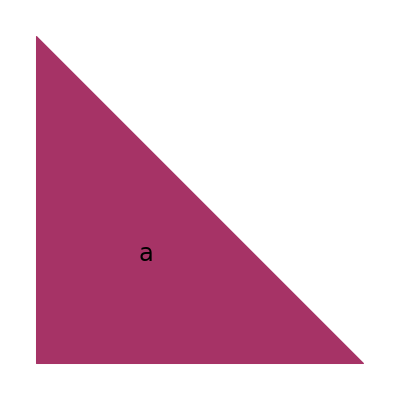
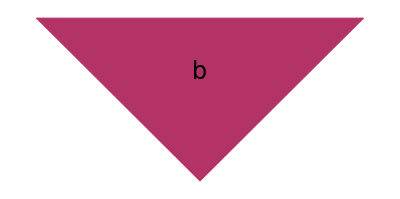
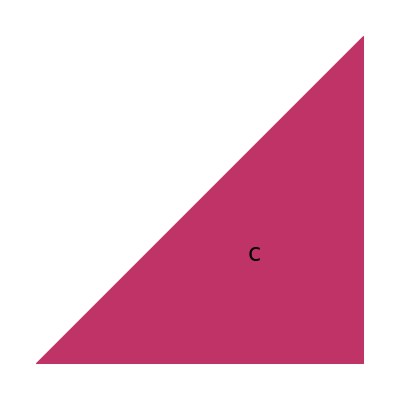
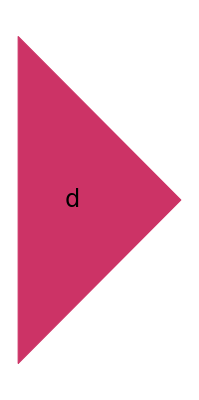
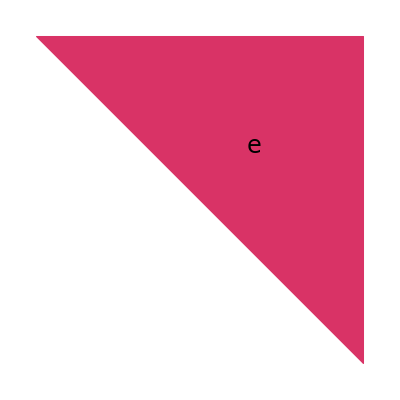
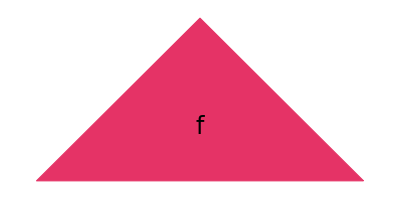
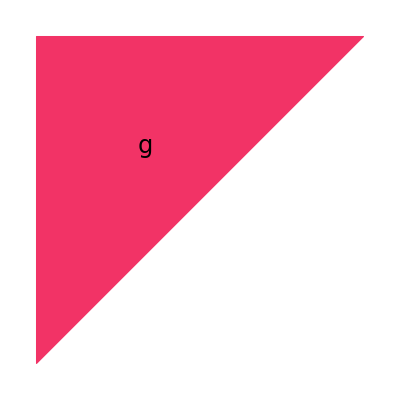
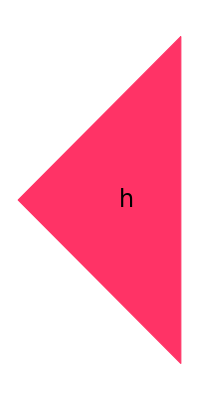

```mathematica
Table[Graphics[polygonsColorsBoundaries[{prototiles⟦i⟧},{i}]],{i,1,Length[prototiles]}]
```

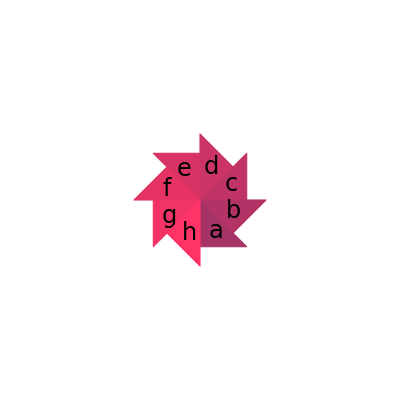

```mathematica
{Graphics[{White,Rectangle[{-7,-7},{7,7}]}],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}//Show
```

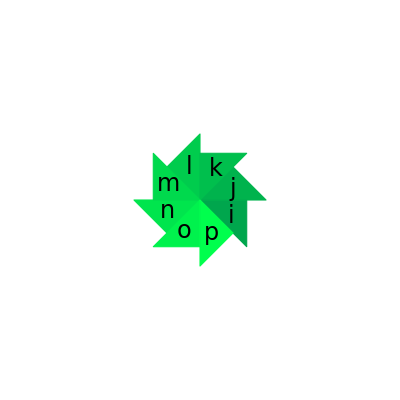

```mathematica
{Graphics[{White,Rectangle[{-7,-7},{7,7}]}],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}//Show
```

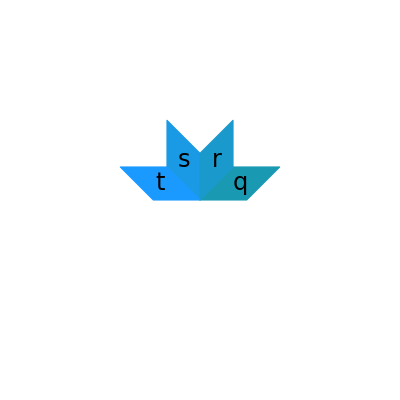

```mathematica
{Graphics[{White,Rectangle[{-7,-7},{7,7}]}],-Graphics-,-Graphics-,-Graphics-,-Graphics-}//Show
```

```mathematica
ComputeLocations=Function[{tiles},Module[{prototileNumber,translation},
Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototiles⟦prototileNumber⟧⟦j⟧+ translation,{j,1,Length[prototiles⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];
```

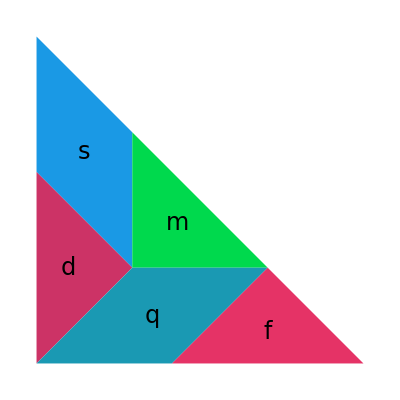
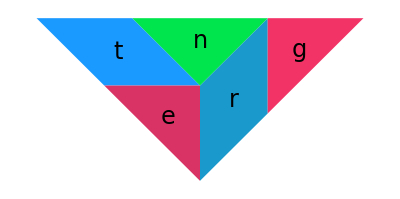
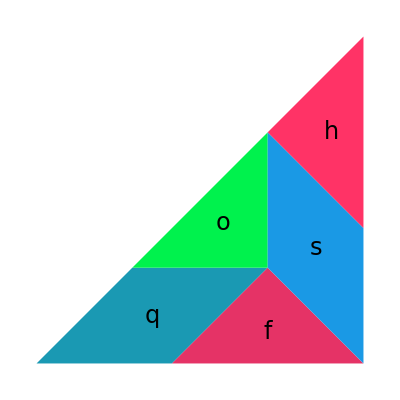
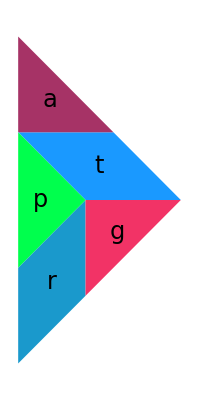
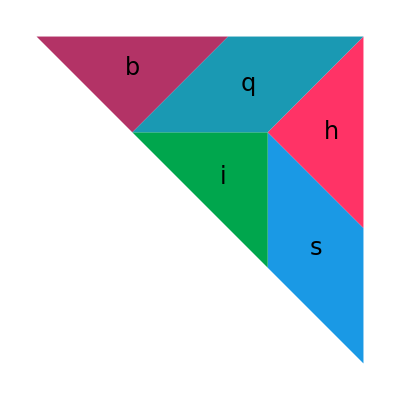
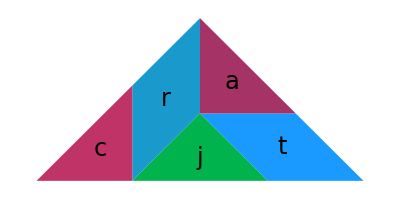
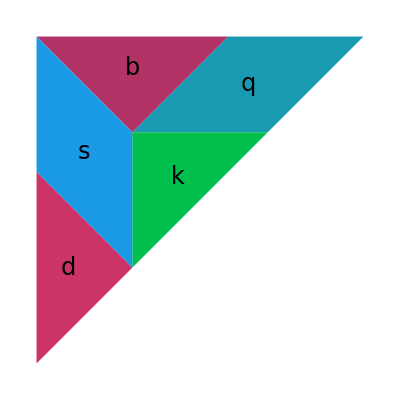
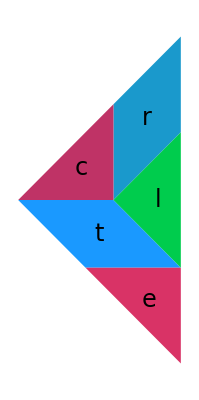

```mathematica
Table[Graphics[polygonsColors[ComputeLocations[wPrototile⟦i⟧],Map[Transpose[#]⟦1⟧&,wPrototile]⟦i⟧]],{i,1,Length[wPrototile]}]
Table[Graphics[polygonsColorsBoundaries[ComputeLocations[wPrototile⟦i⟧],Map[Transpose[#]⟦1⟧&,wPrototile]⟦i⟧]],{i,1,Length[wPrototile]}]
```

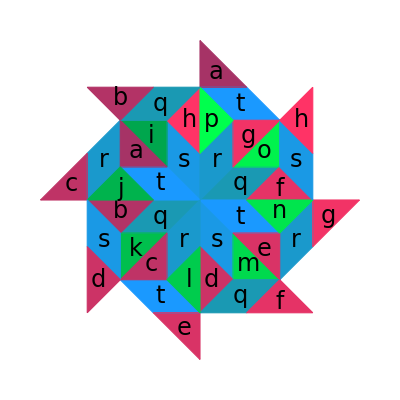

```mathematica
{Graphics[{White,Rectangle[{-7,-7},{7,7}]}],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}//Show
```

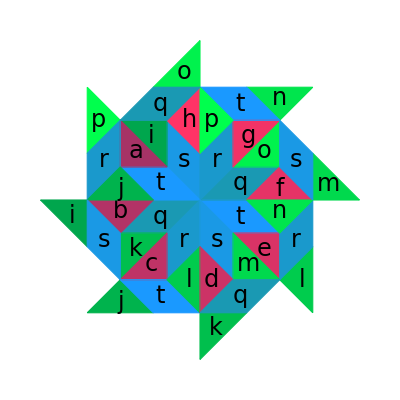

```mathematica
{Graphics[{White,Rectangle[{-7,-7},{7,7}]}],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}//Show
```

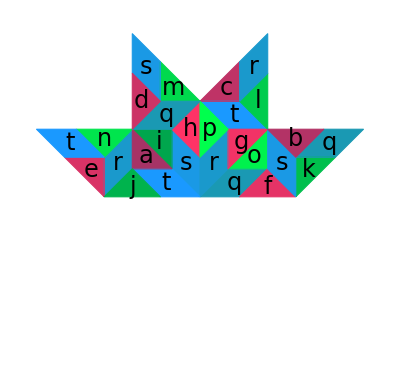

```mathematica
{Graphics[{White,Rectangle[{-7,-7},{7,7}]}],-Graphics-,-Graphics-,-Graphics-,-Graphics-}//Show
```

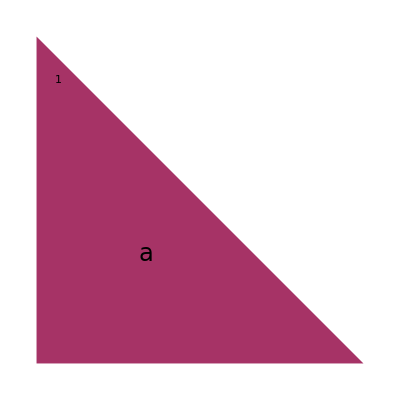
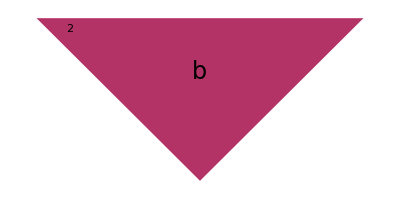
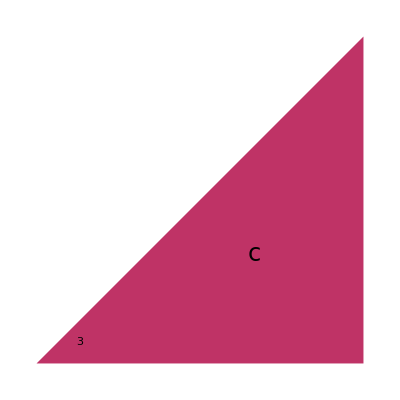
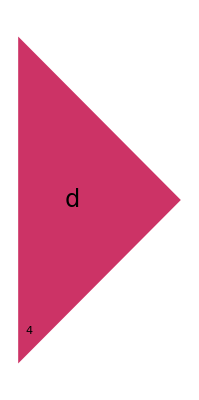
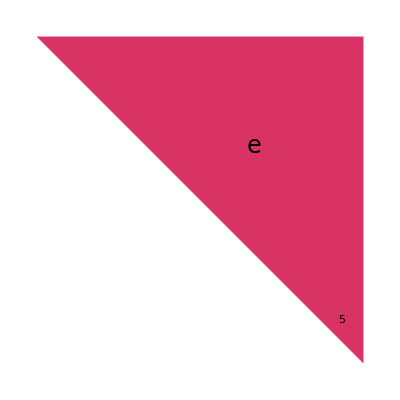
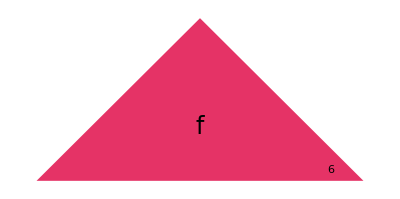
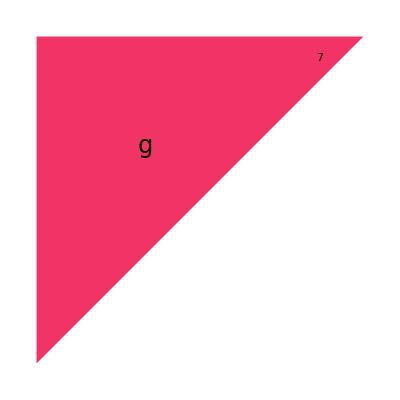
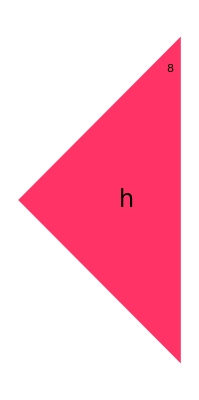

```mathematica
(*Table[Graphics[polygonsColors[{prototiles⟦i⟧},{i}]],{i,1,Length[prototiles]}]*)
Map[drawPrototile,Range[Length[prototiles]]]
```

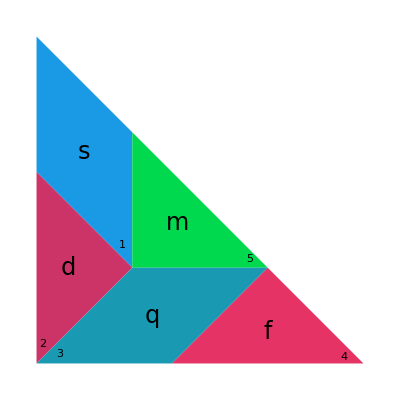
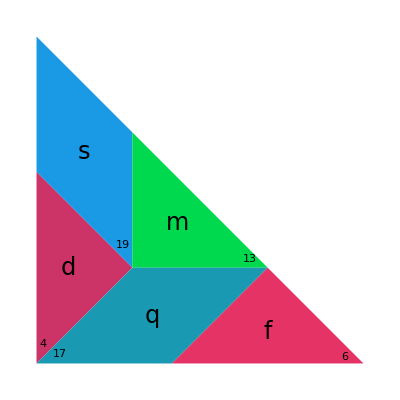
{{-Graphics-,-Graphics-,w(p_1)},{-Graphics-,-Graphics-,w(p_2)},{-Graphics-,-Graphics-,w(p_3)},{-Graphics-,-Graphics-,w(p_4)},{-Graphics-,-Graphics-,w(p_5)},{-Graphics-,-Graphics-,w(p_6)},{-Graphics-,-Graphics-,w(p_7)},{-Graphics-,-Graphics-,w(p_8)},{-Graphics-,-Graphics-,w(p_9)},{-Graphics-,-Graphics-,w(p_10)},{-Graphics-,-Graphics-,w(p_11)},{-Graphics-,-Graphics-,w(p_12)},{-Graphics-,-Graphics-,w(p_13)},{-Graphics-,-Graphics-,w(p_14)},{-Graphics-,-Graphics-,w(p_15)},{-Graphics-,-Graphics-,w(p_16)},{-Graphics-,-Graphics-,w(p_17)},{-Graphics-,-Graphics-,w(p_18)},{-Graphics-,-Graphics-,w(p_19)},{-Graphics-,-Graphics-,w(p_20)}}

```mathematica
Map[drawwPrototile,Range[Length[prototiles]]]
```

## 2.Defining substitution ω(tiles) (run 1)

```mathematica
polygons=Function[polygonCorners,Table[{color⟦Mod[i,Length[color],1]⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]];
polygonsColorsPlain=Function[{polygonCorners,colorsIndices},Table[{color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧]},{i,1,Length[polygonCorners]}]];
polygonsColors=Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Dashing[{0,Medium}]],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧],
Text[Style[label⟦colorsIndices⟦i⟧⟧,Black,24,FontFamily->"Times New Roman",Italic],Total[polygonCorners⟦i⟧]/Length[polygonCorners⟦i⟧]]},
{i,1,Length[polygonCorners]}]];
polygonsColorsBoundariesPlain=polygonsColorsBoundaries=Function[{polygonCorners,colorsIndices},Table[{EdgeForm[Thick],color⟦colorsIndices⟦i⟧⟧,Polygon[polygonCorners⟦i⟧]},
{i,1,Length[polygonCorners]}]];

(*ωTile(tile) = list of tiles which represent the substituted tile  *)
ωTile=Function[tile,Module[{tiles,prototileNumber,translation},
{prototileNumber,translation}=tile;
tiles=wPrototile⟦prototileNumber⟧;
(*tiles +λ translation*)
Table[{tiles⟦i⟧⟦1⟧,tiles⟦i⟧⟦2⟧+ λ translation},{i,1,Length[tiles]}]
]];
(*AddTranslation=Function[{locations,translation},Table[locations⟦i⟧+translation,{i,1,Length[locations]}]];*)
ComputeLocations=Function[{tiles},Module[{prototileNumber,translation},
Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototiles⟦prototileNumber⟧⟦j⟧+ translation,{j,1,Length[prototiles⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];
(*ω substitutes a list of tiles by substituting each tile individually *)
ω=Function[tiles,Flatten[Map[ωTile,tiles],1]]
supertile=Function[{prototileNumber,n},Nest[ω,{{prototileNumber,prototiles⟦prototileNumber⟧⟦1⟧}},n]]

(*maximum number smaller than the limit*)
bsearchMin[list_List,elem_]:=Module[{n0=1,n1=Length[list],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list⟦m⟧==elem,While[list⟦m⟧==elem,m++];
Return[m-1]];
If[list⟦m⟧<elem,n0=m+1,n1=m-1]];
If[list⟦m⟧<elem,m,m-1]];

(*minimum number larger than the limit*)
bsearchMax[list_List,elem_]:=Module[{n0=1,n1=Length[list],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[list[[m]]==elem,While[list[[m]]==elem,m--];
Return[m+1]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
If[list[[m]]>elem,m,m+1]];


varpepsilonZero=10^(-10);
positiveEdgeQ=Function[edgeLocation,Module[{x,y},{x,y}=edgeLocation⟦2⟧-edgeLocation⟦1⟧;If[x>0 || (Abs[x]<varpepsilonZero&&y>0),True,False]]];
(*computeEdgesDirections= {{1,1,1,-1,-1,,,},{1,1,-1,..}} where 1=samedirection, -1 opposite direction *)
computeEdgesDirections=Function[tileLocations,Module[{edge,lastedge},
lastedge={tileLocations⟦Length[tileLocations]⟧,tileLocations⟦1⟧};
Join[Table[edge={tileLocations⟦i⟧,tileLocations⟦i+1⟧};If[positiveEdgeQ[edge]==True,1,-1],{i,1,Length[tileLocations]-1}],If[positiveEdgeQ[lastedge]==True,{1},{-1}]]]];
prototilesDirections=Map[computeEdgesDirections,prototiles]
prototilesLengths=Map[Length,prototiles]

Unflatten=Function[{list,lengths},Module[{k},
k=0;
Table[Table[k++;list⟦k⟧,{i,1,lengths⟦j⟧}],{j,1,Length[lengths]}]]];
swapVerticesofEdge=Function[v1v2,{v1v2⟦2⟧,v1v2⟦1⟧}];

cyclicRange=Function[{interval,n},Module[{a,b},
{a,b}=interval;
If[a≤ b,Range[a,b],
Join[Range[a,n],Range[b]]]]];
drawProtoEdge=Function[protoEdge,Module[{loc},
(*protoEdge={prototilenumber,number of edge on prototile} *)
loc=prototiles⟦protoEdge⟦1⟧⟧;
Graphics[{color⟦protoEdge⟦1⟧⟧,Polygon[loc], Black, Line[{loc⟦protoEdge⟦2⟧⟧,loc⟦Mod[protoEdge⟦2⟧+1,Length[loc],1]⟧}]}]]];
drawProtoVertex=Function[protoVertex,Module[{loc},loc=prototiles⟦protoVertex⟦1⟧⟧;Graphics[{color⟦protoVertex⟦1⟧⟧,Polygon[loc],Black,Point[{loc⟦protoVertex⟦2⟧⟧}]}]]];
```

Function[tiles,Flatten[ωTile/@tiles,1]]

Function[{prototileNumber,n},Nest[ω,{{prototileNumber,prototiles⟦prototileNumber⟧⟦1⟧}},n]]

{{-1,1,-1},{1,1,-1},{1,1,-1},{1,-1,-1},{1,-1,1},{-1,-1,1},{-1,-1,1},{-1,1,1},{1,1,-1},{1,-1,-1},{1,-1,-1},{1,-1,1},{-1,-1,1},{-1,1,1},{-1,1,1},{-1,1,-1},{1,1,-1,-1},{1,1,-1,-1},{1,-1,-1,1},{-1,-1,1,1}}

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4}

```mathematica
(*ω(prototiles)*)
prototiles//Length
(*ω(prototiles)*)
prototiles//Length
Table[Graphics[polygonsColors[ComputeLocations[ωTile[{i,{0,0}}]],Map[#⟦1⟧&,ωTile[{i,{0,0}}]]]],{i,1,Length[prototiles]}]
```

20

20

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Expand[FullSimplify[supertile[1,3]]]
```

{{19,{4+3 √2,-10-7 √2}},{8,{4+3 √2,-8-5 √2}},{17,{2+2 √2,-8-6 √2}},{13,{4+3 √2,-8-5 √2}},{19,{2+3 √2,-8-5 √2}},{4,{2+2 √2,-8-6 √2}},{9,{2+2 √2,-8-6 √2}},{18,{4+2 √2,-6-4 √2}},{3,{2+2 √2,-6-4 √2}},{20,{4+3 √2,-6-5 √2}},{5,{4+3 √2,-8-5 √2}},{12,{4+3 √2,-6-5 √2}},{17,{0,-6-4 √2}},{6,{2+2 √2,-6-4 √2}},{19,{2+2 √2,-6-4 √2}},{11,{2+2 √2,-6-4 √2}},{17,{2+2 √2,-4-4 √2}},{2,{2+√2,-4-3 √2}},{15,{2+√2,-4-3 √2}},{20,{4+3 √2,-4-3 √2}},{1,{2+2 √2,-2-2 √2}},{16,{2+√2,-2-√2}},{18,{2+√2,-4-3 √2}},{10,{2+√2,-4-3 √2}},{19,{2+√2,-4-3 √2}},{8,{2+√2,-2-√2}},{17,{0,-2-2 √2}},{13,{2+√2,-2-√2}},{19,{√2,-2-√2}},{4,{0,-2-2 √2}},{9,{0,-2-2 √2}},{18,{0,-6-4 √2}},{7,{2+√2,-4-3 √2}},{20,{2+√2,-4-3 √2}},{1,{0,-2-2 √2}},{16,{0,-4-2 √2}},{20,{2+√2,-6-5 √2}},{5,{2+√2,-8-5 √2}},{12,{2+2 √2,-8-6 √2}},{18,{2+√2,-8-5 √2}},{14,{2+2 √2,-6-4 √2}},{18,{0,-14-10 √2}},{7,{2+√2,-12-9 √2}},{20,{2+√2,-12-9 √2}},{12,{2+√2,-12-9 √2}},{18,{2,-12-8 √2}},{3,{0,-12-8 √2}},{16,{0,-12-8 √2}},{17,{2+2 √2,-10-8 √2}},{2,{2+√2,-10-7 √2}},{19,{2+2 √2,-12-8 √2}},{4,{2+√2,-12-9 √2}},{11,{2+2 √2,-12-8 √2}},{20,{4+3 √2,-10-7 √2}},{1,{2+2 √2,-8-6 √2}},{18,{2+√2,-10-7 √2}},{14,{2+2 √2,-8-6 √2}},{20,{2+√2,-8-7 √2}},{5,{2+√2,-10-7 √2}},{10,{2+√2,-10-7 √2}},{19,{√2,-8-5 √2}},{4,{0,-8-6 √2}},{17,{0,-8-6 √2}},{6,{2+2 √2,-8-6 √2}},{13,{2+√2,-8-5 √2}},{19,{√2,-10-7 √2}},{4,{0,-10-8 √2}},{11,{0,-12-8 √2}},{17,{0,-10-8 √2}},{13,{2+√2,-10-7 √2}},{17,{0,-14-10 √2}},{6,{2+2 √2,-14-10 √2}},{19,{2+2 √2,-14-10 √2}},{11,{2+2 √2,-14-10 √2}},{17,{2+2 √2,-12-10 √2}},{2,{2+√2,-12-9 √2}},{15,{2+√2,-12-9 √2}},{20,{6+4 √2,-14-10 √2}},{1,{4+3 √2,-12-9 √2}},{18,{4+2 √2,-14-10 √2}},{3,{2+2 √2,-14-10 √2}},{10,{4+2 √2,-14-10 √2}},{19,{6+4 √2,-14-10 √2}},{8,{6+4 √2,-12-8 √2}},{17,{4+3 √2,-12-9 √2}},{13,{6+4 √2,-12-8 √2}},{19,{4+4 √2,-12-8 √2}},{4,{4+3 √2,-12-9 √2}},{9,{4+3 √2,-12-9 √2}},{18,{6+4 √2,-14-10 √2}},{7,{8+5 √2,-12-9 √2}},{14,{8+6 √2,-12-8 √2}},{20,{8+5 √2,-12-9 √2}},{16,{6+4 √2,-12-8 √2}},{17,{6+4 √2,-12-8 √2}},{6,{8+6 √2,-12-8 √2}},{19,{8+6 √2,-12-8 √2}},{11,{8+6 √2,-12-8 √2}},{17,{8+6 √2,-10-8 √2}},{2,{8+5 √2,-10-7 √2}},{15,{8+5 √2,-10-7 √2}},{20,{6+4 √2,-10-8 √2}},{5,{6+4 √2,-12-8 √2}},{18,{6+4 √2,-12-8 √2}},{7,{8+5 √2,-10-7 √2}},{14,{6+5 √2,-10-7 √2}},{18,{4+2 √2,-12-8 √2}},{3,{2+2 √2,-12-8 √2}},{10,{2+√2,-12-9 √2}},{20,{4+3 √2,-12-9 √2}},{12,{4+3 √2,-12-9 √2}},{20,{14+10 √2,-14-10 √2}},{1,{12+9 √2,-12-9 √2}},{18,{12+8 √2,-14-10 √2}},{14,{12+9 √2,-12-9 √2}},{20,{12+8 √2,-12-10 √2}},{5,{12+8 √2,-14-10 √2}},{10,{12+8 √2,-14-10 √2}},{19,{10+8 √2,-12-8 √2}},{4,{10+7 √2,-12-9 √2}},{17,{10+7 √2,-12-9 √2}},{6,{12+9 √2,-12-9 √2}},{13,{12+8 √2,-12-8 √2}},{18,{8+6 √2,-14-10 √2}},{7,{10+7 √2,-12-9 √2}},{20,{10+7 √2,-12-9 √2}},{12,{10+7 √2,-12-9 √2}},{18,{10+6 √2,-12-8 √2}},{3,{8+6 √2,-12-8 √2}},{16,{8+6 √2,-12-8 √2}},{17,{6+4 √2,-14-10 √2}},{6,{8+6 √2,-14-10 √2}},{19,{8+6 √2,-14-10 √2}},{8,{8+6 √2,-12-8 √2}},{15,{8+5 √2,-12-9 √2}},{17,{8+6 √2,-14-10 √2}},{6,{10+8 √2,-14-10 √2}},{13,{12+8 √2,-14-10 √2}},{19,{10+8 √2,-14-10 √2}},{15,{10+7 √2,-12-9 √2}},{20,{10+7 √2,-10-7 √2}},{1,{8+6 √2,-8-6 √2}},{18,{8+5 √2,-10-7 √2}},{14,{8+6 √2,-8-6 √2}},{20,{8+5 √2,-8-7 √2}},{5,{8+5 √2,-10-7 √2}},{10,{8+5 √2,-10-7 √2}},{19,{6+5 √2,-8-5 √2}},{4,{6+4 √2,-8-6 √2}},{17,{6+4 √2,-8-6 √2}},{6,{8+6 √2,-8-6 √2}},{13,{8+5 √2,-8-5 √2}},{19,{4+4 √2,-6-4 √2}},{4,{4+3 √2,-6-5 √2}},{11,{4+3 √2,-8-5 √2}},{17,{4+3 √2,-6-5 √2}},{13,{6+4 √2,-6-4 √2}},{18,{4+3 √2,-10-7 √2}},{7,{6+4 √2,-8-6 √2}},{20,{6+4 √2,-8-6 √2}},{12,{6+4 √2,-8-6 √2}},{18,{6+3 √2,-8-5 √2}},{3,{4+3 √2,-8-5 √2}},{16,{4+3 √2,-8-5 √2}},{17,{4+3 √2,-10-7 √2}},{6,{6+5 √2,-10-7 √2}},{13,{8+5 √2,-10-7 √2}},{19,{6+5 √2,-10-7 √2}},{15,{6+4 √2,-8-6 √2}}}

```mathematica
Map[#[[1]]&,supertile[1,3]]
```

{19,8,17,13,19,4,9,18,3,20,5,12,17,6,19,11,17,2,15,20,1,16,18,10,19,8,17,13,19,4,9,18,7,20,1,16,20,5,12,18,14,18,7,20,12,18,3,16,17,2,19,4,11,20,1,18,14,20,5,10,19,4,17,6,13,19,4,11,17,13,17,6,19,11,17,2,15,20,1,18,3,10,19,8,17,13,19,4,9,18,7,14,20,16,17,6,19,11,17,2,15,20,5,18,7,14,18,3,10,20,12,20,1,18,14,20,5,10,19,4,17,6,13,18,7,20,12,18,3,16,17,6,19,8,15,17,6,13,19,15,20,1,18,14,20,5,10,19,4,17,6,13,19,4,11,17,13,18,7,20,12,18,3,16,17,6,13,19,15}

```mathematica
Graphics[polygonsColors[ComputeLocations[N[supertile[1,2]]],Map[#⟦1⟧&,supertile[1,2]]]]
Graphics[polygonsColors[ComputeLocations[N[supertile[1,3]]],Map[#⟦1⟧&,supertile[1,3]]]]
Graphics[polygonsColors[ComputeLocations[N[supertile[1,4]]],Map[#⟦1⟧&,supertile[1,4]]]]
Graphics[polygonsColorsBoundariesPlain[ComputeLocations[N[supertile[1,5]]],Map[#⟦1⟧&,supertile[1,5]]]]
```

-Graphics-

-Graphics-

## 3.Computing Collared Tiles, stableEdges, collaredVertices (run 1,2)

```mathematica
timingList1={};
tiles=Expand[FullSimplify[supertile[1,5]]];
(*tilesLocations={tile1_written_as_list_of_locations, length of tile2_written_as_list_of_locations,...}. *)
AppendTo[timingList1,Timing[tilesLocations=ComputeLocations[tiles];"tilesLocations"]];
tilesLengths=Map[Length,tilesLocations];
(*tilesLocationsAsEdges={tile1_written_as_list_of_positive_edges, length of tile2_written_as_list_of_positive_edges,...}. A positive edge is a vector starting at the origin and terminating on the I or IV quadrant, excluding the negative y-axis.*)
(*tilesEdgesDirections= directions of each tile where 1= same direction, -1=opposite directions. tile has counterclockwise direction. edge has positive direction.*)
(*AppendTo[timingList1,Timing[tilesEdgesDirections=Map[computeEdgesDirections,tilesLocations];"tilesEdgesDirections"]];*)
AppendTo[timingList1,Timing[tilesEdgesDirections=Map[prototilesDirections⟦#⟦1⟧⟧&,tiles];"tilesEdgesDirections"]];

computePositiveEdgesLocations=Function[{index},Module[{edge,lastedge,tileLocations},
tileLocations=tilesLocations⟦index⟧;
lastedge={tileLocations⟦Length[tileLocations]⟧,tileLocations⟦1⟧};
Join[Table[edge={tileLocations⟦i⟧,tileLocations⟦i+1⟧};If[tilesEdgesDirections⟦index⟧⟦i⟧==1,edge,{edge⟦2⟧,edge⟦1⟧}],{i,1,Length[tileLocations]-1}],If[tilesEdgesDirections⟦index⟧⟦Length[tileLocations]⟧==1,{lastedge},{{lastedge⟦2⟧,lastedge⟦1⟧}}]]]];
AppendTo[timingList1,Timing[tilesLocationsAsEdges=Table[computePositiveEdgesLocations[i],{i,1,Length[tilesLocations]}];"tilesLocationsAsEdges"]];
(*accumulationsOfTilesLengths=Accumulate[{length of tile1_written_as_list_of_positive_edges, length of tile2_written_as_list_positive_edges,... }]*)
accumulationsOfTilesLengths=Accumulate[tilesLengths];
(*tilesLocationsAsEdgesFlattened = list of all edges as pairs of locations (in the supertile)*)
tilesLocationsAsEdgesFlattened=Flatten[tilesLocationsAsEdges,1];
(*commonTilesLocationsAsEdgesIndices gives keysE and edgesToEdgesOfTiles (read below)*)
AppendTo[timingList1,Timing[positionIndexOftilesLocationsAsEdgesFlattened=Normal[PositionIndex[tilesLocationsAsEdgesFlattened]];"positionIndexOftilesLocationsAsEdgesFlattened"]];
(*edgesLocations = unique positive edges (i.e. the location of the positive edge is unique) *)
edgesLocations=Keys[positionIndexOftilesLocationsAsEdgesFlattened];
(*edgesToEdgesOfTiles = {{i1,i2},{i3,i4}...} where the positive edges at i1,i2, in tilesLocationsAsEdgesFlattened are the same.  *)
edgesToEdgesOfTiles=Values[positionIndexOftilesLocationsAsEdgesFlattened];
(*if {i1,i2} has length 2 then the edge at i1,i2 is an interior edge of the supertile. If it has length 1 then it is a bounded edge of the supertile:*)
{bEdges,iEdges}=Values[Sort[Normal[PositionIndex[Map[Length,edgesToEdgesOfTiles]]]]];
(*{bEdges,iEdges}=Values[PositionIndex[Map[Length,edgesToEdgesOfTiles]]];*)
iEdgesToEdgesOfTiles=edgesToEdgesOfTiles[[iEdges]];
bEdgesToEdgesOfTiles=edgesToEdgesOfTiles[[bEdges]];
iEdgesToSingletEdges=Map[#⟦1⟧&,iEdgesToEdgesOfTiles];
iEdgesLocations=tilesLocationsAsEdgesFlattened[[iEdgesToSingletEdges]];
bEdgesLocations=tilesLocationsAsEdgesFlattened[[Flatten[bEdgesToEdgesOfTiles]]];
(*  The tiling T contains the supertile; thus interior edges of the supertile are edges of the tiling T.
 An edge of the tiling T is a pair {(tile,indexOfEdgeInPrototile),(tile,indexOfEdgeInPrototile)}.
 edgeAsPairsOfPrototileNumbers =  {{prototileNumber,indexOfEdgeInPrototile},{prototileNumber,indexOfEdgeInPrototile}} Dictionary-sorted.
iEdgesAsPairsOfPrototileNumbers =  { Sort({prototileNumber,indexOfEdgeInPrototile},{prototileNumber,indexOfEdgeInPrototile}),...} !!This list has lots of multiplicities! *)
(*an interior edge in the supertile is a pair of edges that have common locations*)
bsearchMaxInaccumulationsOfTilesLengths[elem_]:=Module[{n0=1,n1=Length[accumulationsOfTilesLengths],m},While[n0≤n1,m=Floor[(n0+n1)/2];
If[accumulationsOfTilesLengths[[m]]==elem,While[accumulationsOfTilesLengths[[m]]==elem,m--];
Return[m+1]];
If[accumulationsOfTilesLengths[[m]]<elem,n0=m+1,n1=m-1]];
If[accumulationsOfTilesLengths[[m]]>elem,m,m+1]];

Clear[t1,i1,t2,i2]
unflattentedgeflattened=Function[tedgeflattenedNumber,Module[{tileNumber},
tileNumber=bsearchMaxInaccumulationsOfTilesLengths[tedgeflattenedNumber];
{tileNumber,If[tileNumber==1, tedgeflattenedNumber, tedgeflattenedNumber-accumulationsOfTilesLengths⟦tileNumber-1⟧]}]];
iEdgesAsPairsOfTiles=Map[Apply[Sort[{unflattentedgeflattened[#1],unflattentedgeflattened[#2]}]&,#]&,iEdgesToEdgesOfTiles];
iEdgesAsPairsOfPrototileNumbers=Table[{{t1,i1},{t2,i2}}=iEdgesAsPairsOfTiles⟦i⟧;Sort[{{tiles⟦t1⟧⟦1⟧,i1},{tiles⟦t2⟧⟦1⟧,i2}}],{i,1,Length[iEdgesAsPairsOfTiles]}];
Clear[t1,i1,t2,i2]
```

```mathematica
Take[tiles,10]//ColumnForm
tilesLocationsAsEdges//Length
```

{19,{24+17 √2,-58-41 √2}}
{8,{24+17 √2,-56-39 √2}}
{17,{22+16 √2,-56-40 √2}}
{13,{24+17 √2,-56-39 √2}}
{19,{22+17 √2,-56-39 √2}}
{4,{22+16 √2,-56-40 √2}}
{9,{22+16 √2,-56-40 √2}}
{18,{24+16 √2,-54-38 √2}}
{3,{22+16 √2,-54-38 √2}}
{20,{24+17 √2,-54-39 √2}}

5741

```mathematica
timingList1//ColumnForm
```

{0.14646,tilesLocations}
{0.00805,tilesEdgesDirections}
{0.20836,tilesLocationsAsEdges}
{0.03507,positionIndexOftilesLocationsAsEdgesFlattened}

```mathematica
Graphics[Line[bEdgesLocations]]
Graphics[Line[iEdgesLocations]]
```

-Graphics-

```mathematica
(*iEdgesAsPairsOfPrototileNumbers[[3]]
tilesLocationsAsEdges[[1]]
tilesLocationsAsEdges[[1]][[3]]
tilesLocationsAsEdges[[3]]
tilesLocationsAsEdges[[3]][[6]]*)
```

```mathematica
Show[Graphics[polygonsColors[ComputeLocations[supertile[1,4]],Map[#⟦1⟧&,supertile[1,4]]]],Graphics[Line[iEdgesLocations]]]
```

```mathematica
(*drawiEdges=Function[ieNum,Graphics[{polygons[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Line[iEdgesLocations⟦ieNum⟧]}]];*)
drawiEdges=Function[ieNum,Graphics[{polygonsColors[Map[tilesLocations⟦#⟦1⟧⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,iEdgesAsPairsOfTiles⟦ieNum⟧]],Line[iEdgesLocations⟦ieNum⟧]}]];
drawiEdges[1]
```

-Graphics-

```mathematica
iEdgesRepresentatives=Map[#⟦1⟧&,Values[PositionIndex[iEdgesAsPairsOfPrototileNumbers]]];
iEdgesRepresentatives//Length
sEdges=iEdgesAsPairsOfPrototileNumbers⟦iEdgesRepresentatives⟧
drawsEdges=Function[i,drawiEdges[iEdgesRepresentatives⟦i⟧]];
drawWsEdges=Function[seNum,Module[{se,wse},
se=Map[#⟦1⟧&,iEdgesAsPairsOfTiles⟦iEdgesRepresentatives⟦seNum⟧⟧];
wse=Flatten[Map[ωTile[tiles⟦#⟧]&,se],1];
Graphics[Join[polygonsColors[ComputeLocations[wse],Map[#⟦1⟧&,wse]],Map[Line,λ ComputeLocations[tiles⟦se⟧]]]]]];
```

56

{{{18,4},{19,1}},{{8,2},{19,2}},{{9,2},{19,3}},{{19,4},{20,1}},{{8,1},{17,2}},{{8,3},{16,1}},{{9,3},{17,1}},{{13,3},{17,3}},{{4,1},{17,4}},{{5,3},{13,1}},{{13,2},{19,1}},{{19,2},{20,3}},{{18,2},{19,3}},{{4,2},{19,4}},{{4,3},{12,1}},{{1,3},{9,1}},{{12,2},{18,1}},{{17,2},{18,3}},{{3,2},{18,4}},{{3,1},{20,2}},{{3,3},{11,1}},{{12,3},{20,1}},{{5,2},{20,4}},{{5,1},{11,3}},{{17,1},{20,2}},{{6,2},{17,2}},{{15,2},{17,3}},{{17,4},{18,1}},{{6,1},{19,4}},{{6,3},{14,1}},{{11,3},{19,1}},{{2,1},{19,2}},{{15,3},{19,3}},{{11,2},{17,1}},{{17,3},{20,4}},{{2,2},{17,4}},{{2,3},{10,1}},{{7,3},{15,1}},{{1,2},{20,2}},{{10,2},{20,3}},{{1,1},{18,2}},{{16,2},{18,3}},{{2,1},{16,3}},{{10,3},{18,1}},{{7,2},{18,2}},{{7,1},{20,4}},{{16,3},{20,3}},{{1,1},{15,3}},{{14,2},{20,1}},{{5,1},{18,4}},{{6,1},{12,3}},{{14,3},{18,3}},{{8,1},{14,3}},{{3,1},{9,3}},{{7,1},{13,3}},{{4,1},{10,3}}}

```mathematica
(*sEdges*)
iEdgesRepresentatives//Length
Map[drawiEdges,iEdgesRepresentatives]
```

56

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
xxx=Map[drawiEdges,iEdgesRepresentatives];
yyy=Table[Style[StringForm["se_(``)=",i],18],{i,1,Length[xxx]}];
Grid[Partition[Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,1,Length[xxx]}],5],Frame->All]
Grid[{Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,56,Length[xxx]}]},Frame->All]
```

se_1=
-Graphics- | se_2=
-Graphics- | se_3=
-Graphics- | se_4=
-Graphics- | se_5=
-Graphics-
se_6=
-Graphics- | se_7=
-Graphics- | se_8=
-Graphics- | se_9=
-Graphics- | se_10=
-Graphics-
se_11=
-Graphics- | se_12=
-Graphics- | se_13=
-Graphics- | se_14=
-Graphics- | se_15=
-Graphics-
se_16=
-Graphics- | se_17=
-Graphics- | se_18=
-Graphics- | se_19=
-Graphics- | se_20=
-Graphics-
se_21=
-Graphics- | se_22=
-Graphics- | se_23=
-Graphics- | se_24=
-Graphics- | se_25=
-Graphics-
se_26=
-Graphics- | se_27=
-Graphics- | se_28=
-Graphics- | se_29=
-Graphics- | se_30=
-Graphics-
se_31=
-Graphics- | se_32=
-Graphics- | se_33=
-Graphics- | se_34=
-Graphics- | se_35=
-Graphics-
se_36=
-Graphics- | se_37=
-Graphics- | se_38=
-Graphics- | se_39=
-Graphics- | se_40=
-Graphics-
se_41=
-Graphics- | se_42=
-Graphics- | se_43=
-Graphics- | se_44=
-Graphics- | se_45=
-Graphics-
se_46=
-Graphics- | se_47=
-Graphics- | se_48=
-Graphics- | se_49=
-Graphics- | se_50=
-Graphics-
se_51=
-Graphics- | se_52=
-Graphics- | se_53=
-Graphics- | se_54=
-Graphics- | se_55=
-Graphics-

se_56=
-Graphics-

```mathematica
prototiles//Length
```

20

```mathematica
(*iedgesLocationsAsVertices={positive_edge1, positive_edge2,...}, where these edges are interior edges of the supertile written as positive edges and their location is unique. A positive edge is a vector starting at the origin and terminating on the I or IV quadrant, excluding the negative y-axis.*)
iedgesLocationsAsVertices=iEdgesLocations;
(*iedgesLocationsAsVerticesFlattened = all possible vertices as locations (coming from the interior edges in the supertile)*)
iedgesLocationsAsVerticesFlattened=Flatten[iedgesLocationsAsVertices,1];
(*commonVerticesIndicesInEdgesLocationsAsVertices gives keysV and valuesV (read below)*)
positionIndexOfiedgesLocationsAsVerticesFlattened=PositionIndex[iedgesLocationsAsVerticesFlattened];
(*keysV = unique vertices (their location is unique) *)
verticesLocations=Keys[positionIndexOfiedgesLocationsAsVerticesFlattened];(*representatives of common locations of the vertices*)
(*valuesV = {{i1,i2...},{j3,j4...}...} where the vertices at i1,i2, in iedgesLocationsAsVerticesFlattened are the same. The goal is to obtain the edges with common vertices  *)
verticesToVerticesOfiEdges=Values[positionIndexOfiedgesLocationsAsVerticesFlattened];(* indices of keysV*)
(*if {i1,i2..} has length >1 then the vertex at i1,i2... is an interior vertex of the interior_edges of the supertile. 
If it has length 1 then it is a boundary vertex of the interior_edges of the supertile:*)

{boundaryVertices,interiorVertices}=Values[Sort[Normal[PositionIndex[Map[Length[#]>MAXDegreeOfBoundaryVertices&,verticesToVerticesOfiEdges]]]]];
interiorVerticesToVerticesOfiEdges=verticesToVerticesOfiEdges[[interiorVertices]];
boundaryVerticesToVerticesOfiEdges=verticesToVerticesOfiEdges[[boundaryVertices]];
interiorVerticesToSingleVerticesOfiEdges=Map[#⟦1⟧&,interiorVerticesToVerticesOfiEdges];
interiorVerticesLocations=iedgesLocationsAsVerticesFlattened[[interiorVerticesToSingleVerticesOfiEdges]];
boundaryVerticesLocations=iedgesLocationsAsVerticesFlattened[[Flatten[boundaryVerticesToVerticesOfiEdges]]];
tileNumberEdgeVertexTotileNumberVertex=Function[tileNumberEdgeVertex,Module[{tileNumber,edgeNumberOnTile,vertexNumberOnEdge,initialOrFinalVertexOnEdge,edgeDirection,vertexNumberOnTile},
{{tileNumber,edgeNumberOnTile},vertexNumberOnEdge}=tileNumberEdgeVertex;
edgeDirection=tilesEdgesDirections[[tileNumber]][[edgeNumberOnTile]];
vertexNumberOnTile=edgeNumberOnTile;
If[(edgeDirection==1 && vertexNumberOnEdge==2)||(edgeDirection==-1 && vertexNumberOnEdge==1),vertexNumberOnTile=Mod[vertexNumberOnTile+1,tilesLengths[[tileNumber]],1]];
{tileNumber,vertexNumberOnTile}]];

unflatteniEvertexflattened=Function[ievertexflattenedNumber,
{IntegerPart[(ievertexflattenedNumber+1)/2],Mod[ievertexflattenedNumber,2,1]}];
(*verticesAsListOfIndicesOfTiles={ (iEdgesAsPairsOfPrototileNumbers[positive_edge_i_index], 1 or 2 = initial or final vertex in positive_edge_i ),...}*)
interiorVerticesAsiEdges=Table[Sort[Table[unflatteniEvertexflattened[interiorVerticesToVerticesOfiEdges⟦j⟧⟦i⟧],{i,1,Length[interiorVerticesToVerticesOfiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesToVerticesOfiEdges]}];

(*protoVerticesAsListOfIndicesOfEdges={ (positive_edge_i_index, 1 or 2 = initial or final vertex in positive_edge_i ),...}*)
verticesAsListOfTilesEVNumbers=Table[Sort[Table[
{iEdgeNumber,index}=interiorVerticesAsiEdges⟦j⟧⟦i⟧;
{iEdgesAsPairsOfTiles⟦iEdgeNumber⟧,index},{i,1,Length[interiorVerticesToVerticesOfiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesToVerticesOfiEdges]}];

verticesAsListOfTilesVNumbers=Table[Union[Flatten[Table[{{e1,e2},v}=verticesAsListOfTilesEVNumbers[[j]][[i]];
{tileNumberEdgeVertexTotileNumberVertex[{e1,v}],
tileNumberEdgeVertexTotileNumberVertex[{e2,v}]},{i,1,Length[verticesAsListOfTilesEVNumbers[[j]]]}],1]],{j,1,Length[verticesAsListOfTilesEVNumbers]}];

verticesAsListOfPrototileEVNumbers=Table[Sort[Table[
{iEdgeNumber,index}=interiorVerticesAsiEdges⟦j⟧⟦i⟧;
{iEdgesAsPairsOfPrototileNumbers⟦iEdgeNumber⟧,index},
{i,1,Length[interiorVerticesAsiEdges⟦j⟧]}]],{j,1,Length[interiorVerticesAsiEdges]}];

verticesAsListOfPrototileVNumbers=Table[Sort[Table[
{tileNumber,index}=verticesAsListOfTilesVNumbers⟦j⟧⟦i⟧;
{tiles⟦tileNumber⟧⟦1⟧,index},
{i,1,Length[verticesAsListOfTilesVNumbers⟦j⟧]}]],{j,1,Length[verticesAsListOfTilesVNumbers]}];
```

```mathematica
verticesAsListOfPrototileVNumbers//Tally//Length
Take[verticesAsListOfPrototileVNumbers//Tally,10]//ColumnForm
```

49

{{{17,1},{17,3},{18,1},{18,3},{19,1},{19,3},{20,1},{20,3}},100}
{{{8,3},{16,2},{18,4},{19,2}},196}
{{{8,2},{9,3},{17,2},{19,3}},160}
{{{1,3},{9,2},{19,4},{20,2}},190}
{{{3,1},{5,1},{8,1},{11,1},{13,1},{16,1},{17,3},{20,3}},36}
{{{1,1},{4,1},{6,1},{9,1},{12,1},{14,1},{17,1},{18,3}},36}
{{{4,2},{13,3},{17,4},{19,1}},189}
{{{5,3},{13,2},{19,2},{20,4}},210}
{{{3,1},{6,1},{11,1},{14,1},{18,3},{19,1},{19,3},{20,3}},30}
{{{4,3},{12,2},{18,2},{19,4}},210}

```mathematica
(*boundary vertices should be shown in RED. Interior vertices in Black *)
Show[Graphics[{Red,Point[boundaryVerticesLocations]}],
Graphics[Point[interiorVerticesLocations]],Graphics[Line[iEdgesLocations]]]
```

-Graphics-

```mathematica
iEdgesToEdgesOfTiles[[{1,2,5}]]==edgesToEdgesOfTiles[[iEdges[[{1,2,5}]]]]

iedgesLocationsAsVertices[[{1,2,5}]]==tilesLocationsAsEdgesFlattened[[Map[#[[1]]&,iEdgesToEdgesOfTiles[[{1,2,5}]]]]]

iedgesLocationsAsVertices[[{1,2,5}]]==tilesLocationsAsEdgesFlattened[[Map[#[[1]]&,edgesToEdgesOfTiles[[iEdges[[{1,2,5}]]]]]]]
```

True

True

True

```mathematica
(*drawInteriorVertex=Function[ivNum,Graphics[{polygons[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]}]];*)
drawInteriorVertex=Function[ivNum,Graphics[{polygonsColors[Map[tilesLocations⟦#⟦1⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧],Map[tiles⟦#⟦1⟧⟧⟦1⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]],
Point[Map[tilesLocations⟦#⟦1⟧⟧⟦#⟦2⟧⟧&,verticesAsListOfTilesVNumbers⟦ivNum⟧]]}]];
drawInteriorVertex[3]
```

-Graphics-

```mathematica
iVerticesRepresentatives=Map[#⟦1⟧&,Values[PositionIndex[verticesAsListOfPrototileVNumbers]]];
iVerticesRepresentatives//Length
cVertices=verticesAsListOfPrototileVNumbers⟦iVerticesRepresentatives⟧
drawcVertices=Function[index,drawInteriorVertex[iVerticesRepresentatives⟦index⟧]];
drawWcVertices=Function[cvNum,Module[{cv,wcv},
cv=Map[#⟦1⟧&,verticesAsListOfTilesVNumbers⟦iVerticesRepresentatives⟦cvNum⟧⟧];
wcv=Flatten[Map[ωTile[tiles⟦#⟧]&,cv],1];
Graphics[Join[polygonsColors[ComputeLocations[wcv],Map[#⟦1⟧&,wcv]],Map[Line,λ ComputeLocations[tiles⟦cv⟧]]]]]];
```

49

{{{17,1},{17,3},{18,1},{18,3},{19,1},{19,3},{20,1},{20,3}},{{8,3},{16,2},{18,4},{19,2}},{{8,2},{9,3},{17,2},{19,3}},{{1,3},{9,2},{19,4},{20,2}},{{3,1},{5,1},{8,1},{11,1},{13,1},{16,1},{17,3},{20,3}},{{1,1},{4,1},{6,1},{9,1},{12,1},{14,1},{17,1},{18,3}},{{4,2},{13,3},{17,4},{19,1}},{{5,3},{13,2},{19,2},{20,4}},{{3,1},{6,1},{11,1},{14,1},{18,3},{19,1},{19,3},{20,3}},{{4,3},{12,2},{18,2},{19,4}},{{3,2},{12,3},{18,1},{20,2}},{{3,3},{11,2},{17,2},{18,4}},{{4,1},{5,2},{11,3},{12,1},{17,1},{20,1}},{{6,3},{14,2},{17,2},{20,2}},{{6,2},{15,3},{17,3},{19,4}},{{7,3},{15,2},{17,4},{18,2}},{{2,2},{11,3},{17,1},{19,2}},{{2,1},{7,1},{10,1},{15,1},{18,1},{19,1},{19,3},{20,1}},{{2,3},{10,2},{17,4},{20,4}},{{1,2},{10,3},{18,2},{20,3}},{{1,1},{2,2},{9,1},{16,3},{17,1},{18,3}},{{2,1},{5,1},{8,1},{10,1},{13,1},{16,1},{17,3},{18,1}},{{1,1},{4,1},{7,1},{9,1},{12,1},{15,1},{17,1},{20,1}},{{7,2},{16,3},{18,3},{20,4}},{{1,2},{8,1},{15,3},{16,1},{17,3},{20,3}},{{5,2},{14,3},{18,4},{20,1}},{{5,1},{6,2},{12,3},{13,1},{17,3},{18,1}},{{1,1},{6,1},{9,1},{14,1},{17,1},{18,1},{18,3},{19,1}},{{3,1},{6,1},{8,1},{11,1},{14,1},{16,1},{19,1},{20,3}},{{7,1},{8,2},{14,3},{15,1},{19,3},{20,1}},{{8,1},{16,1},{17,1},{17,3},{18,1},{19,1},{20,1},{20,3}},{{1,1},{3,1},{6,1},{9,1},{11,1},{14,1},{18,3},{19,1}},{{2,1},{4,1},{7,1},{10,1},{12,1},{15,1},{19,3},{20,1}},{{1,1},{4,1},{9,1},{12,1},{17,1},{17,3},{18,3},{20,1}},{{2,1},{3,2},{9,3},{10,1},{18,1},{19,3}},{{5,1},{8,1},{13,1},{16,1},{17,1},{17,3},{18,1},{20,3}},{{2,1},{5,1},{7,1},{10,1},{13,1},{15,1},{18,1},{19,3}},{{6,1},{7,2},{13,3},{14,1},{18,3},{19,1}},{{3,1},{4,2},{10,3},{11,1},{19,1},{20,3}},{{4,1},{7,1},{12,1},{15,1},{17,1},{19,3},{20,1},{20,3}},{{5,1},{13,1},{17,1},{17,3},{18,1},{18,3},{19,3},{20,3}},{{2,1},{5,1},{10,1},{13,1},{17,3},{18,1},{18,3},{19,3}},{{4,1},{12,1},{17,1},{17,3},{18,3},{19,3},{20,1},{20,3}},{{3,1},{8,1},{11,1},{16,1},{17,3},{19,1},{20,1},{20,3}},{{1,1},{9,1},{17,1},{17,3},{18,1},{18,3},{19,1},{20,1}},{{3,1},{11,1},{17,3},{18,3},{19,1},{19,3},{20,1},{20,3}},{{6,1},{14,1},{17,1},{18,1},{18,3},{19,1},{19,3},{20,3}},{{2,1},{10,1},{17,3},{18,1},{18,3},{19,1},{19,3},{20,1}},{{7,1},{15,1},{17,1},{18,1},{19,1},{19,3},{20,1},{20,3}}}

```mathematica
(* protovertices == collared vertices *)
iVerticesRepresentatives//Length
Map[drawInteriorVertex,iVerticesRepresentatives]
```

49

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
xxx=Map[drawInteriorVertex,iVerticesRepresentatives];
yyy=Table[Style[StringForm["sv_(``)=",i],18],{i,1,Length[xxx]}];
Grid[Partition[Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,1,Length[xxx]}],5],Frame->All]
Grid[{Table[ColumnForm[{yyy[[i]],xxx[[i]]}],{i,46,Length[xxx]}]},Frame->All]
```

sv_1=
-Graphics- | sv_2=
-Graphics- | sv_3=
-Graphics- | sv_4=
-Graphics- | sv_5=
-Graphics-
sv_6=
-Graphics- | sv_7=
-Graphics- | sv_8=
-Graphics- | sv_9=
-Graphics- | sv_10=
-Graphics-
sv_11=
-Graphics- | sv_12=
-Graphics- | sv_13=
-Graphics- | sv_14=
-Graphics- | sv_15=
-Graphics-
sv_16=
-Graphics- | sv_17=
-Graphics- | sv_18=
-Graphics- | sv_19=
-Graphics- | sv_20=
-Graphics-
sv_21=
-Graphics- | sv_22=
-Graphics- | sv_23=
-Graphics- | sv_24=
-Graphics- | sv_25=
-Graphics-
sv_26=
-Graphics- | sv_27=
-Graphics- | sv_28=
-Graphics- | sv_29=
-Graphics- | sv_30=
-Graphics-
sv_31=
-Graphics- | sv_32=
-Graphics- | sv_33=
-Graphics- | sv_34=
-Graphics- | sv_35=
-Graphics-
sv_36=
-Graphics- | sv_37=
-Graphics- | sv_38=
-Graphics- | sv_39=
-Graphics- | sv_40=
-Graphics-
sv_41=
-Graphics- | sv_42=
-Graphics- | sv_43=
-Graphics- | sv_44=
-Graphics- | sv_45=
-Graphics-

sv_46=
-Graphics- | sv_47=
-Graphics- | sv_48=
-Graphics- | sv_49=
-Graphics-

### results

```mathematica
sEdges
```

{{{18,4},{19,1}},{{8,2},{19,2}},{{9,2},{19,3}},{{19,4},{20,1}},{{8,1},{17,2}},{{8,3},{16,1}},{{9,3},{17,1}},{{13,3},{17,3}},{{4,1},{17,4}},{{5,3},{13,1}},{{13,2},{19,1}},{{19,2},{20,3}},{{18,2},{19,3}},{{4,2},{19,4}},{{4,3},{12,1}},{{1,3},{9,1}},{{12,2},{18,1}},{{17,2},{18,3}},{{3,2},{18,4}},{{3,1},{20,2}},{{3,3},{11,1}},{{12,3},{20,1}},{{5,2},{20,4}},{{5,1},{11,3}},{{17,1},{20,2}},{{6,2},{17,2}},{{15,2},{17,3}},{{17,4},{18,1}},{{6,1},{19,4}},{{6,3},{14,1}},{{11,3},{19,1}},{{2,1},{19,2}},{{15,3},{19,3}},{{11,2},{17,1}},{{17,3},{20,4}},{{2,2},{17,4}},{{2,3},{10,1}},{{7,3},{15,1}},{{1,2},{20,2}},{{10,2},{20,3}},{{1,1},{18,2}},{{16,2},{18,3}},{{2,1},{16,3}},{{10,3},{18,1}},{{7,2},{18,2}},{{7,1},{20,4}},{{16,3},{20,3}},{{1,1},{15,3}},{{14,2},{20,1}},{{5,1},{18,4}},{{6,1},{12,3}},{{14,3},{18,3}},{{8,1},{14,3}},{{3,1},{9,3}},{{7,1},{13,3}},{{4,1},{10,3}}}

```mathematica
cVertices
```

{{{17,1},{17,3},{18,1},{18,3},{19,1},{19,3},{20,1},{20,3}},{{8,3},{16,2},{18,4},{19,2}},{{8,2},{9,3},{17,2},{19,3}},{{1,3},{9,2},{19,4},{20,2}},{{3,1},{5,1},{8,1},{11,1},{13,1},{16,1},{17,3},{20,3}},{{1,1},{4,1},{6,1},{9,1},{12,1},{14,1},{17,1},{18,3}},{{4,2},{13,3},{17,4},{19,1}},{{5,3},{13,2},{19,2},{20,4}},{{3,1},{6,1},{11,1},{14,1},{18,3},{19,1},{19,3},{20,3}},{{4,3},{12,2},{18,2},{19,4}},{{3,2},{12,3},{18,1},{20,2}},{{3,3},{11,2},{17,2},{18,4}},{{4,1},{5,2},{11,3},{12,1},{17,1},{20,1}},{{6,3},{14,2},{17,2},{20,2}},{{6,2},{15,3},{17,3},{19,4}},{{7,3},{15,2},{17,4},{18,2}},{{2,2},{11,3},{17,1},{19,2}},{{2,1},{7,1},{10,1},{15,1},{18,1},{19,1},{19,3},{20,1}},{{2,3},{10,2},{17,4},{20,4}},{{1,2},{10,3},{18,2},{20,3}},{{1,1},{2,2},{9,1},{16,3},{17,1},{18,3}},{{2,1},{5,1},{8,1},{10,1},{13,1},{16,1},{17,3},{18,1}},{{1,1},{4,1},{7,1},{9,1},{12,1},{15,1},{17,1},{20,1}},{{7,2},{16,3},{18,3},{20,4}},{{1,2},{8,1},{15,3},{16,1},{17,3},{20,3}},{{5,2},{14,3},{18,4},{20,1}},{{5,1},{6,2},{12,3},{13,1},{17,3},{18,1}},{{1,1},{6,1},{9,1},{14,1},{17,1},{18,1},{18,3},{19,1}},{{3,1},{6,1},{8,1},{11,1},{14,1},{16,1},{19,1},{20,3}},{{7,1},{8,2},{14,3},{15,1},{19,3},{20,1}},{{8,1},{16,1},{17,1},{17,3},{18,1},{19,1},{20,1},{20,3}},{{1,1},{3,1},{6,1},{9,1},{11,1},{14,1},{18,3},{19,1}},{{2,1},{4,1},{7,1},{10,1},{12,1},{15,1},{19,3},{20,1}},{{1,1},{4,1},{9,1},{12,1},{17,1},{17,3},{18,3},{20,1}},{{2,1},{3,2},{9,3},{10,1},{18,1},{19,3}},{{5,1},{8,1},{13,1},{16,1},{17,1},{17,3},{18,1},{20,3}},{{2,1},{5,1},{7,1},{10,1},{13,1},{15,1},{18,1},{19,3}},{{6,1},{7,2},{13,3},{14,1},{18,3},{19,1}},{{3,1},{4,2},{10,3},{11,1},{19,1},{20,3}},{{4,1},{7,1},{12,1},{15,1},{17,1},{19,3},{20,1},{20,3}},{{5,1},{13,1},{17,1},{17,3},{18,1},{18,3},{19,3},{20,3}},{{2,1},{5,1},{10,1},{13,1},{17,3},{18,1},{18,3},{19,3}},{{4,1},{12,1},{17,1},{17,3},{18,3},{19,3},{20,1},{20,3}},{{3,1},{8,1},{11,1},{16,1},{17,3},{19,1},{20,1},{20,3}},{{1,1},{9,1},{17,1},{17,3},{18,1},{18,3},{19,1},{20,1}},{{3,1},{11,1},{17,3},{18,3},{19,1},{19,3},{20,1},{20,3}},{{6,1},{14,1},{17,1},{18,1},{18,3},{19,1},{19,3},{20,3}},{{2,1},{10,1},{17,3},{18,1},{18,3},{19,1},{19,3},{20,1}},{{7,1},{15,1},{17,1},{18,1},{19,1},{19,3},{20,1},{20,3}}}

```mathematica
sEdges//Length
cVertices//Length
```

56

49

## 4. Exponential Matrix, Index Matrix (run 1,2,3)

```mathematica
(*exponential matrix*)
cVerticesAssEdges=verticesAsListOfPrototileEVNumbers[[iVerticesRepresentatives]];
sEdgescVerticesMatrix=ConstantArray[0,{Length[sEdges],Length[cVertices]}];

sEdgescVerticesMatrixIndicesFunction=
Function[cvNumber,Module[{cv,se,vInitialOrFinal,seNumber,value},
cv=cVerticesAssEdges⟦cvNumber⟧;
Table[{se,vInitialOrFinal}=cv⟦i⟧;
seNumber=Position[sEdges,se]⟦1⟧⟦1⟧;
value=If[vInitialOrFinal==1,-1,1];
sEdgescVerticesMatrix⟦seNumber⟧⟦cvNumber⟧+=value;
{{seNumber,cvNumber},value},{i,1,Length[cv]}]]];


sEdgescVerticesMatrixIndices=Table[sEdgescVerticesMatrixIndicesFunction[i],{i,1,Length[cVertices]}];
(*stableEdges-collardVertices Matrix (se1=-cv1+cv9+cv14...*)
Print["δ^0=",sEdgescVerticesMatrix//MatrixForm]
```

δ^0=(-1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | -1 | -1
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1
0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(*Index Matrix*)
prototilessEdgesMatrix=ConstantArray[0,{Length[prototiles],Length[sEdges]}];
Table[{{p1,e1},{p2,e2}}=sEdges⟦sedgeNumber⟧;
prototilessEdgesMatrix⟦p1⟧⟦sedgeNumber⟧+=prototilesDirections⟦p1⟧⟦e1⟧;
prototilessEdgesMatrix⟦p2⟧⟦sedgeNumber⟧+=prototilesDirections⟦p2⟧⟦e2⟧;,
{sedgeNumber,1,Length[sEdges]}];
Print["δ^1=",prototilessEdgesMatrix//MatrixForm]
```

δ^1=(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0
1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
prototilessEdgesMatrix.sEdgescVerticesMatrix//Max
prototilessEdgesMatrix.sEdgescVerticesMatrix//Min
```

0

0

## 5. Homotopy matrices Wv, We, Wf

```mathematica
(*Homotopy ω(prototile) --> prototile : Hverticesp1t1 is the image of the map on the vertices from ω(prototile) to same protitile 1.*)


Hverticesp1t1={2,1,1,1};
Hverticesp1t2={2,2,1};
Hverticesp1t3={2,2,3,2};
Hverticesp1t4={3,3,2};
Hverticesp1t5={3,1,2};

Hverticesp2t1={3,1,1,1};
Hverticesp2t2={2,3,1};
Hverticesp2t3={2,3,2};
Hverticesp2t4={2,3,3,3};
Hverticesp2t5={3,1,3};

Hverticesp3t1={1,1,1,1};
Hverticesp3t2={2,1,1};
Hverticesp3t3={2,3,4,1};
Hverticesp3t4={2,3,3};
Hverticesp3t5={3,3,3,3};
Hverticesp3t6={4,3,3};
Hverticesp3t7={4,1,1};

Hverticesp1={1,{Hverticesp1t1,Hverticesp1t2,Hverticesp1t3,Hverticesp1t4,Hverticesp1t5}};
Hverticesp2={1,{Hverticesp2t1,Hverticesp2t2,Hverticesp2t3,Hverticesp2t4,Hverticesp2t5}};
Hverticesp3={1,{Hverticesp3t1,Hverticesp3t2,Hverticesp3t3,Hverticesp3t4,Hverticesp3t5,Hverticesp3t6,Hverticesp3t7}};

Hvertices={Hverticesp1,Hverticesp1,Hverticesp1,Hverticesp1,Hverticesp1,Hverticesp1,Hverticesp1,Hverticesp1,
Hverticesp2,Hverticesp2,Hverticesp2,Hverticesp2,Hverticesp2,Hverticesp2,Hverticesp2,Hverticesp2,
Hverticesp3,Hverticesp3,Hverticesp3,Hverticesp3}


Hvertices⟦3⟧⟦2⟧⟦1⟧=RotateLeft[Hvertices⟦3⟧⟦2⟧⟦1⟧,2]
Hvertices⟦4⟧=Hvertices⟦3⟧

Hvertices⟦5⟧⟦2⟧⟦1⟧=RotateLeft[Hvertices⟦5⟧⟦2⟧⟦1⟧,2]
Hvertices⟦5⟧⟦2⟧⟦3⟧=RotateLeft[Hvertices⟦5⟧⟦2⟧⟦3⟧,2]
Hvertices⟦6⟧=Hvertices⟦5⟧

Hvertices⟦7⟧⟦2⟧⟦3⟧=RotateLeft[Hvertices⟦7⟧⟦2⟧⟦3⟧,2]
Hvertices⟦8⟧=Hvertices⟦7⟧

Hvertices⟦10⟧⟦2⟧⟦1⟧=RotateLeft[Hvertices⟦10⟧⟦2⟧⟦1⟧,2]
Hvertices⟦11⟧=Hvertices⟦10⟧

Hvertices⟦12⟧⟦2⟧⟦1⟧=RotateLeft[Hvertices⟦12⟧⟦2⟧⟦1⟧,2]
Hvertices⟦12⟧⟦2⟧⟦4⟧=RotateLeft[Hvertices⟦12⟧⟦2⟧⟦4⟧,2]
Hvertices⟦13⟧=Hvertices⟦12⟧

Hvertices⟦14⟧⟦2⟧⟦4⟧=RotateLeft[Hvertices⟦14⟧⟦2⟧⟦4⟧,2]
Hvertices⟦15⟧=Hvertices⟦14⟧

Hvertices⟦19⟧⟦2⟧⟦3⟧=RotateLeft[Hvertices⟦19⟧⟦2⟧⟦3⟧,2]
Hvertices⟦20⟧=Hvertices⟦19⟧

Table[Map[Length,Map[#⟦2⟧&,Hvertices]⟦i⟧],{i,1,Length[Hvertices]}]==Map[prototilesLengths⟦#⟧&,wPrototileNumbers]
```

{{1,{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}},{1,{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}},{1,{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}},{1,{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}},{1,{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}},{1,{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}},{1,{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}},{1,{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}},{1,{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}},{1,{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}},{1,{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}},{1,{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}},{1,{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}},{1,{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}},{1,{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}},{1,{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}},{1,{{1,1,1,1},{2,1,1},{2,3,4,1},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}}},{1,{{1,1,1,1},{2,1,1},{2,3,4,1},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}}},{1,{{1,1,1,1},{2,1,1},{2,3,4,1},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}}},{1,{{1,1,1,1},{2,1,1},{2,3,4,1},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}}}}

{1,1,2,1}

{1,{{1,1,2,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}}}

{1,1,2,1}

{3,2,2,2}

{1,{{1,1,2,1},{2,2,1},{3,2,2,2},{3,3,2},{3,1,2}}}

{3,2,2,2}

{1,{{2,1,1,1},{2,2,1},{3,2,2,2},{3,3,2},{3,1,2}}}

{1,1,3,1}

{1,{{1,1,3,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}}}

{1,1,3,1}

{3,3,2,3}

{1,{{1,1,3,1},{2,3,1},{2,3,2},{3,3,2,3},{3,1,3}}}

{3,3,2,3}

{1,{{3,1,1,1},{2,3,1},{2,3,2},{3,3,2,3},{3,1,3}}}

{4,1,2,3}

{1,{{1,1,1,1},{2,1,1},{4,1,2,3},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}}}

True

```mathematica
HverticesSimple=Map[#⟦2⟧&,Hvertices]
```

{{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}},{{2,1,1,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}},{{1,1,2,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}},{{1,1,2,1},{2,2,1},{2,2,3,2},{3,3,2},{3,1,2}},{{1,1,2,1},{2,2,1},{3,2,2,2},{3,3,2},{3,1,2}},{{1,1,2,1},{2,2,1},{3,2,2,2},{3,3,2},{3,1,2}},{{2,1,1,1},{2,2,1},{3,2,2,2},{3,3,2},{3,1,2}},{{2,1,1,1},{2,2,1},{3,2,2,2},{3,3,2},{3,1,2}},{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}},{{1,1,3,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}},{{1,1,3,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}},{{1,1,3,1},{2,3,1},{2,3,2},{3,3,2,3},{3,1,3}},{{1,1,3,1},{2,3,1},{2,3,2},{3,3,2,3},{3,1,3}},{{3,1,1,1},{2,3,1},{2,3,2},{3,3,2,3},{3,1,3}},{{3,1,1,1},{2,3,1},{2,3,2},{3,3,2,3},{3,1,3}},{{3,1,1,1},{2,3,1},{2,3,2},{2,3,3,3},{3,1,3}},{{1,1,1,1},{2,1,1},{2,3,4,1},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}},{{1,1,1,1},{2,1,1},{2,3,4,1},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}},{{1,1,1,1},{2,1,1},{4,1,2,3},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}},{{1,1,1,1},{2,1,1},{4,1,2,3},{2,3,3},{3,3,3,3},{4,3,3},{4,1,1}}}

```mathematica
drawHomotopyVerticesOfTilesNoGraphics=Function[tile,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
imageVertices=HverticesSimple⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]];

drawHomotopyVerticesOfTilesNoGraphics=Function[tile,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
imageVertices=HverticesSimple⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{arrows}]];

drawHomotopycVertices=Function[cVertexNum,Module[{cv},
cv=cVertices⟦cVertexNum⟧;
Graphics[Map[drawHomotopyVerticesOfTilesNoGraphics,Table[{cv⟦i,1⟧,Expand[FullSimplify[prototiles⟦cv⟦i,1⟧,1⟧-prototiles⟦cv⟦i,1⟧,cv⟦i,2⟧⟧]]},{i,1,Length[cv]}]]]]];

drawHomotopyVerticesOfTiles=Function[tile,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[ωTile[tile]];
imageVertices=HverticesSimple⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{tile}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
Graphics[{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]]];

drawHomotopyVertices=Function[prototilenumber,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
imageVertices=HverticesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[{Thick,Arrowheads[0.03],Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]]},{i,1,Length[imageVertices]}];
Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}]
]];

drawHomotopyVerticesAll=Function[prototilenumber,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
imageVertices=HverticesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}],
Table[Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows⟦i⟧}],{i,1,Length[arrows]}]}]];

drawHomotopyVerticesAll=Function[prototilenumber,Module[{locs,imageloc,arrows,imageVertices},
locs=ComputeLocations[wPrototile⟦prototilenumber⟧];
imageVertices=HverticesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocations[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[Partition[Riffle[locs⟦i⟧,imageloc⟦imageVertices⟦i⟧⟧],2]],{i,1,Length[imageVertices]}];
{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}],
Table[Graphics[{arrows⟦i⟧}],{i,1,Length[arrows]}]}]];
```

```mathematica
Table[drawHomotopyVerticesAll[i],{i,1,Length[prototiles]}]//ColumnForm
```

```mathematica
Table[drawHomotopyVertices[i],{i,1,Length[prototiles]}]
```

```mathematica
Table[drawHomotopycVertices[i],{i,1,Length[cVertices]}]
```

```mathematica
homotopycVertices=ConstantArray[0,Length[cVertices]];

Clear[cv,ps,vs,locsH,xx,yy,ts,cvNum]
For[cvNum=1,cvNum≤ Length[cVertices],cvNum++,
cv=cVertices⟦cvNum⟧;
cvHpreimage=Table[Position[HverticesSimple⟦cv⟦i,1⟧⟧,cv⟦i,2⟧],{i,1,Length[cv]}];
{ps,vs}=Transpose[cv];
ts=Table[{ps⟦i⟧,prototiles⟦ps⟦i⟧⟧⟦1⟧-prototiles⟦ps⟦i⟧⟧⟦vs⟦i⟧⟧},{i,1,Length[ps]}];
(*Map[ωTile,ts]*)
locsH=Table[Expand[FullSimplify[ComputeLocations[ωTile[ts⟦i⟧]]]],{i,1,Length[ts]}];
cvHpreimageLocations=Table[Table[locsH⟦j⟧⟦cvHpreimage⟦j⟧⟦i,1⟧,cvHpreimage⟦j⟧⟦i,2⟧⟧,{i,1,Length[cvHpreimage⟦j⟧]}],{j,1,Length[cvHpreimage]}];
(*cvHpreimage//ColumnForm*)
(*cvHpreimageLocations//Point//Graphics*)
(*Flatten[cvHpreimageLocations,1]*)
cvHpreimageFlattened=Flatten[cvHpreimage,1];
(*cvHpreimageFlattenedTiles=Flatten[Table[ConstantArray[i,Length[cvHpreimage⟦i⟧]],{i,1,Length[cvHpreimage]}],1]*)
cvHpreimageFlattenedPrototiles=Flatten[Table[ConstantArray[ps[[i]],Length[cvHpreimage⟦i⟧]],{i,1,Length[cvHpreimage]}],1];
hcverticesindices=Values[Normal[PositionIndex[Flatten[cvHpreimageLocations,1]]]];

(*hcverticesAsTiles=Table[
xx=cvHpreimageFlattened⟦hcverticesindices⟦j⟧⟧;
yy=cvHpreimageFlattenedTiles⟦hcverticesindices⟦j⟧⟧;
Sort[Table[Flatten[{yy⟦i⟧,xx⟦i⟧}],{i,1,Length[xx]}]],{j,1,Length[hcverticesindices]}]
Table[Map[locsH⟦#⟦1⟧,#⟦2⟧,#⟦3⟧⟧&,hcverticesAsTiles⟦i⟧],{i,1,Length[hcverticesAsTiles]}]*)

hcvertices=Table[
xx=cvHpreimageFlattened⟦hcverticesindices⟦j⟧⟧;
yy=cvHpreimageFlattenedPrototiles⟦hcverticesindices⟦j⟧⟧;
Sort[Table[{wPrototileNumbers⟦yy⟦i⟧⟧⟦xx⟦i,1⟧⟧,xx⟦i,2⟧},{i,1,Length[xx]}]],{j,1,Length[hcverticesindices]}];
homotopycVertices⟦cvNum⟧=Table[Position[cVertices,hcvertices⟦i⟧]⟦1,1⟧,{i,1,Length[hcvertices]}]]
homotopycVertices
```

{{1,14,15,16,17,12,19,24,2,11,10,3,4,7,8,20,26},{13,5},{11,9,8,26,10,7},{27,6},{1,14,16,2,4,10,12,19,8,17,26},{8,1,10,16,2,4,19,14,12,15,11},{24,18,4,20,2,3},{21,22},{1,14,16,4,19,2,12,11,10,3,7,8,26},{25,23},{15,28,2,3,16,24},{30,29},{31,16,2,3,19,24,14,4,15,20},{35,32},{20,34,12,11,19,17},{39,33},{26,36,16,24,14,15},{14,1,8,12,19,16,10,24,2,3,4,7,20},{38,37},{7,40,14,15,8,26},{8,41,10,26,16,14,7,12,15,11},{14,1,8,2,4,10,12,16,19,17,24},{8,1,10,16,2,12,19,14,4,15,20},{17,42,10,7,12,11},{7,43,14,10,12,11,19,8,17,26},{3,44,19,17,4,20},{45,2,4,20,12,3,16,19,17,24},{8,1,10,4,19,14,12,15,16,24,2,11,3},{1,14,16,4,19,10,12,2,8,3,26},{12,46,19,11,8,17,4,10,7,20},{10,1,12,8,14,15,16,17,19,24,2,3,4,20,26},{8,1,10,14,16,4,19,2,12,11,3},{14,1,8,16,2,12,19,4,10,7,20},{8,1,10,16,2,14,4,15,17,12,19,11,20},{14,47,8,15,2,26,10,16,24,7},{1,2,4,10,12,19,8,14,15,16,17,24,26},{14,1,8,2,4,12,19,16,10,24,7},{48,4,19,17,10,20,2,12,11,3},{49,14,16,24,4,15,8,2,3,26},{1,16,2,12,19,4,10,14,15,7,8,20,26},{1,2,4,19,14,15,16,17,12,24,11,10,7,8,26},{14,1,8,2,4,16,19,17,12,24,11,10,7},{1,16,2,4,14,15,17,12,19,11,10,7,8,20,26},{1,14,16,10,12,2,8,17,19,3,4,20,26},{8,1,10,14,15,16,17,12,19,24,2,11,3,4,20},{1,14,16,2,17,12,19,11,10,3,4,7,8,20,26},{1,4,19,12,14,15,16,24,2,11,10,3,7,8,26},{14,1,8,16,17,12,19,24,2,11,10,3,4,7,20},{12,1,19,10,14,15,16,24,2,3,4,7,8,20,26}}

```mathematica
cverticesHMtx=ConstantArray[0,{Length[cVertices],Length[cVertices]}];
Table[Table[cverticesHMtx⟦homotopycVertices⟦i⟧⟦j⟧⟧⟦i⟧+=1,{j,1,Length[homotopycVertices⟦i⟧]}],{i,1,Length[homotopycVertices]}];
Print["W_V=",cverticesHMtx//MatrixForm]
```

W_V=(1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
drawHomotopycVertices[2]
Map[drawcVertices,{13,5}]
```

-Graphics-

{-Graphics-,-Graphics-}

```mathematica
drawHomotopycVertices[1]
Map[drawcVertices,{1,14,15,16,17,12,19,24,2,11,10,3,4,7,8,20,26}]
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
protoEdgesAsPairsVerticesFunction=Function[protoedgesIndices,Table[{protoedgesIndices⟦i⟧,protoedgesIndices⟦Mod[i+1,Length[protoedgesIndices],1]⟧},{i,1,Length[protoedgesIndices]}]];
protoEdgesAsPosPairsVerticesFunction=Function[{protoedgesIndices,protoedgesOrientations},Table[If[protoedgesOrientations⟦i⟧==1,{protoedgesIndices⟦i⟧,protoedgesIndices⟦Mod[i+1,Length[protoedgesIndices],1]⟧},{protoedgesIndices⟦Mod[i+1,Length[protoedgesIndices],1]⟧,protoedgesIndices⟦i⟧}],{i,1,Length[protoedgesIndices]}]];


(*initialVertexOfsEdgeNumFunction=Function[sedgeNum,initialVertexOfsEdgeFunction[sEdges⟦sedgeNum⟧]];
finalVertexOfsEdgeNumFunction=Function[sedgeNum,finalVertexOfsEdgeFunction[sEdges⟦sedgeNum⟧]];

initialVertexOfsEdgeFunction=Function[sedge,Sort[{{sedge⟦1⟧⟦1⟧,protoEdgesAsPosPairsVertices⟦sedge⟦1⟧⟦1⟧,sedge⟦1⟧⟦2⟧⟧⟦1⟧},{sedge⟦2⟧⟦1⟧,protoEdgesAsPosPairsVertices⟦sedge⟦2⟧⟦1⟧,sedge⟦2⟧⟦2⟧⟧⟦1⟧}}]];
finalVertexOfsEdgeFunction=Function[sedge,Sort[{{sedge⟦1⟧⟦1⟧,protoEdgesAsPosPairsVertices⟦sedge⟦1⟧⟦1⟧,sedge⟦1⟧⟦2⟧⟧⟦2⟧},{sedge⟦2⟧⟦1⟧,protoEdgesAsPosPairsVertices⟦sedge⟦2⟧⟦1⟧,sedge⟦2⟧⟦2⟧⟧⟦2⟧}}]];
rowForm=Function[lst,{lst}//MatrixForm];
*)

protoVertices=Map[Range,prototilesLengths];

protoEdgesAsPairsOfVertices=Table[protoEdgesAsPairsVerticesFunction[protoVertices⟦i⟧],{i,1,Length[prototiles]}]
protoEdgesAsPosPairsOfVertices=Table[protoEdgesAsPosPairsVerticesFunction[protoVertices⟦i⟧,prototilesDirections⟦i⟧],{i,1,Length[prototiles]}]
wPrototileAsprotoEdgesAsPosPairsOfVertices=Map[protoEdgesAsPosPairsOfVertices⟦#⟧&,wPrototileNumbers];
```

{{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2},{2,3},{3,4},{4,1}},{{1,2},{2,3},{3,4},{4,1}}}

{{{2,1},{2,3},{1,3}},{{1,2},{2,3},{1,3}},{{1,2},{2,3},{1,3}},{{1,2},{3,2},{1,3}},{{1,2},{3,2},{3,1}},{{2,1},{3,2},{3,1}},{{2,1},{3,2},{3,1}},{{2,1},{2,3},{3,1}},{{1,2},{2,3},{1,3}},{{1,2},{3,2},{1,3}},{{1,2},{3,2},{1,3}},{{1,2},{3,2},{3,1}},{{2,1},{3,2},{3,1}},{{2,1},{2,3},{3,1}},{{2,1},{2,3},{3,1}},{{2,1},{2,3},{1,3}},{{1,2},{2,3},{4,3},{1,4}},{{1,2},{2,3},{4,3},{1,4}},{{1,2},{3,2},{4,3},{4,1}},{{2,1},{3,2},{3,4},{4,1}}}

```mathematica
(* FOR OCTAGONAL:
Hedgesp1t1={1,0,0,1};
Hedgesp1t2={0,1,1};
Hedgesp1t3={0,2,2,0};
Hedgesp1t4={0,2,2};
Hedgesp1t5={3,1,2};

Hedgesp2t1={3,0,0,3};
Hedgesp2t2={2,3,1};
Hedgesp2t3={2,2,0};
Hedgesp2t4={2,0,0,2};
Hedgesp2t5={3,3,0};

Hedgesp3t1={0,0,0,0};
Hedgesp3t2={1,0,1};
Hedgesp3t3={2,3,4,1};
Hedgesp3t4={2,0,2};
Hedgesp3t5={0,0,0,0};
Hedgesp3t6={3,0,3};
Hedgesp3t7={4,0,4};

Hedgesp1={1,{Hedgesp1t1,Hedgesp1t2,Hedgesp1t3,Hedgesp1t4,Hedgesp1t5}};
Hedgesp2={1,{Hedgesp2t1,Hedgesp2t2,Hedgesp2t3,Hedgesp2t4,Hedgesp2t5}};
Hedgesp3={1,{Hedgesp3t1,Hedgesp3t2,Hedgesp3t3,Hedgesp3t4,Hedgesp3t5,Hedgesp3t6,Hedgesp3t7}};

Hedges={Hedgesp1,Hedgesp1,Hedgesp1,Hedgesp1,Hedgesp1,Hedgesp1,Hedgesp1,Hedgesp1,
Hedgesp2,Hedgesp2,Hedgesp2,Hedgesp2,Hedgesp2,Hedgesp2,Hedgesp2,Hedgesp2,
Hedgesp3,Hedgesp3,Hedgesp3,Hedgesp3}


Hedges⟦3⟧⟦2⟧⟦1⟧=RotateLeft[Hedges⟦3⟧⟦2⟧⟦1⟧,2]
Hedges⟦4⟧=Hedges⟦3⟧

Hedges⟦5⟧⟦2⟧⟦1⟧=RotateLeft[Hedges⟦5⟧⟦2⟧⟦1⟧,2]
Hedges⟦5⟧⟦2⟧⟦3⟧=RotateLeft[Hedges⟦5⟧⟦2⟧⟦3⟧,2]
Hedges⟦6⟧=Hedges⟦5⟧

Hedges⟦7⟧⟦2⟧⟦3⟧=RotateLeft[Hedges⟦7⟧⟦2⟧⟦3⟧,2]
Hedges⟦8⟧=Hedges⟦7⟧

Hedges⟦10⟧⟦2⟧⟦1⟧=RotateLeft[Hedges⟦10⟧⟦2⟧⟦1⟧,2]
Hedges⟦11⟧=Hedges⟦10⟧

Hedges⟦12⟧⟦2⟧⟦1⟧=RotateLeft[Hedges⟦12⟧⟦2⟧⟦1⟧,2]
Hedges⟦12⟧⟦2⟧⟦4⟧=RotateLeft[Hedges⟦12⟧⟦2⟧⟦4⟧,2]
Hedges⟦13⟧=Hedges⟦12⟧

Hedges⟦14⟧⟦2⟧⟦4⟧=RotateLeft[Hedges⟦14⟧⟦2⟧⟦4⟧,2]
Hedges⟦15⟧=Hedges⟦14⟧

Hedges⟦19⟧⟦2⟧⟦3⟧=RotateLeft[Hedges⟦19⟧⟦2⟧⟦3⟧,2]
Hedges⟦20⟧=Hedges⟦19⟧
HedgesOLD=Hedges

Table[Map[Length,Map[#⟦2⟧&,Hedges]⟦i⟧],{i,1,Length[Hedges]}]==Map[prototilesLengths⟦#⟧&,wPrototileNumbers]
*)
```

```mathematica
HedgesSameDirFunction=Function[{HverticesOfTile,tNumImage},
Table[If[Mod[HverticesOfTile⟦i⟧+1,prototilesLengths⟦tNumImage⟧,1]==HverticesOfTile⟦Mod[i+1,Length[HverticesOfTile],1]⟧,HverticesOfTile⟦i⟧,0],{i,1,Length[HverticesOfTile]}]];
HedgesOppositeDirFunction=Function[{HverticesOfTile,tNumImage},
Table[If[Mod[HverticesOfTile⟦i⟧-1,prototilesLengths⟦tNumImage⟧,1]==HverticesOfTile⟦Mod[i+1,Length[HverticesOfTile],1]⟧,Mod[HverticesOfTile⟦i⟧-1,prototilesLengths⟦tNumImage⟧,1],0],{i,1,Length[HverticesOfTile]}]];
joinSameOppDirHedgesFunction=Function[{sameDirHedges,oppDirHedges},
Table[Table[If[sameDirHedges⟦i⟧⟦j⟧≠0 &&oppDirHedges⟦i⟧⟦j⟧≠0,Print["Error:HedgeHasMultipleValues at {i,j}",{i,j}]];
If[sameDirHedges⟦i⟧⟦j⟧≠0,sameDirHedges⟦i⟧⟦j⟧,oppDirHedges⟦i⟧⟦j⟧],{j,1,Length[sameDirHedges⟦i⟧]}],{i,1,Length[sameDirHedges]}]];
```

```mathematica
HedgesTemp=Table[
sameDirHedges=Map[HedgesSameDirFunction[#,tNum]&,HverticesSimple⟦tNum⟧];
oppDirHedges=Map[HedgesOppositeDirFunction[#,tNum]&,HverticesSimple⟦tNum⟧];
joinSameOppDirHedgesFunction[sameDirHedges,oppDirHedges],{tNum,1,Length[prototiles]}];
Hedges=Table[{1,HedgesTemp⟦i⟧},{i,1,Length[HedgesTemp]}]
```

{{1,{{1,0,0,1},{0,1,1},{0,2,2,0},{0,2,2},{3,1,2}}},{1,{{1,0,0,1},{0,1,1},{0,2,2,0},{0,2,2},{3,1,2}}},{1,{{0,1,1,0},{0,1,1},{0,2,2,0},{0,2,2},{3,1,2}}},{1,{{0,1,1,0},{0,1,1},{0,2,2,0},{0,2,2},{3,1,2}}},{1,{{0,1,1,0},{0,1,1},{2,0,0,2},{0,2,2},{3,1,2}}},{1,{{0,1,1,0},{0,1,1},{2,0,0,2},{0,2,2},{3,1,2}}},{1,{{1,0,0,1},{0,1,1},{2,0,0,2},{0,2,2},{3,1,2}}},{1,{{1,0,0,1},{0,1,1},{2,0,0,2},{0,2,2},{3,1,2}}},{1,{{3,0,0,3},{2,3,1},{2,2,0},{2,0,0,2},{3,3,0}}},{1,{{0,3,3,0},{2,3,1},{2,2,0},{2,0,0,2},{3,3,0}}},{1,{{0,3,3,0},{2,3,1},{2,2,0},{2,0,0,2},{3,3,0}}},{1,{{0,3,3,0},{2,3,1},{2,2,0},{0,2,2,0},{3,3,0}}},{1,{{0,3,3,0},{2,3,1},{2,2,0},{0,2,2,0},{3,3,0}}},{1,{{3,0,0,3},{2,3,1},{2,2,0},{0,2,2,0},{3,3,0}}},{1,{{3,0,0,3},{2,3,1},{2,2,0},{0,2,2,0},{3,3,0}}},{1,{{3,0,0,3},{2,3,1},{2,2,0},{2,0,0,2},{3,3,0}}},{1,{{0,0,0,0},{1,0,1},{2,3,4,1},{2,0,2},{0,0,0,0},{3,0,3},{4,0,4}}},{1,{{0,0,0,0},{1,0,1},{2,3,4,1},{2,0,2},{0,0,0,0},{3,0,3},{4,0,4}}},{1,{{0,0,0,0},{1,0,1},{4,1,2,3},{2,0,2},{0,0,0,0},{3,0,3},{4,0,4}}},{1,{{0,0,0,0},{1,0,1},{4,1,2,3},{2,0,2},{0,0,0,0},{3,0,3},{4,0,4}}}}

```mathematica
HedgesSimple=Map[#⟦2⟧&,Hedges]
```

{{{1,0,0,1},{0,1,1},{0,2,2,0},{0,2,2},{3,1,2}},{{1,0,0,1},{0,1,1},{0,2,2,0},{0,2,2},{3,1,2}},{{0,1,1,0},{0,1,1},{0,2,2,0},{0,2,2},{3,1,2}},{{0,1,1,0},{0,1,1},{0,2,2,0},{0,2,2},{3,1,2}},{{0,1,1,0},{0,1,1},{2,0,0,2},{0,2,2},{3,1,2}},{{0,1,1,0},{0,1,1},{2,0,0,2},{0,2,2},{3,1,2}},{{1,0,0,1},{0,1,1},{2,0,0,2},{0,2,2},{3,1,2}},{{1,0,0,1},{0,1,1},{2,0,0,2},{0,2,2},{3,1,2}},{{3,0,0,3},{2,3,1},{2,2,0},{2,0,0,2},{3,3,0}},{{0,3,3,0},{2,3,1},{2,2,0},{2,0,0,2},{3,3,0}},{{0,3,3,0},{2,3,1},{2,2,0},{2,0,0,2},{3,3,0}},{{0,3,3,0},{2,3,1},{2,2,0},{0,2,2,0},{3,3,0}},{{0,3,3,0},{2,3,1},{2,2,0},{0,2,2,0},{3,3,0}},{{3,0,0,3},{2,3,1},{2,2,0},{0,2,2,0},{3,3,0}},{{3,0,0,3},{2,3,1},{2,2,0},{0,2,2,0},{3,3,0}},{{3,0,0,3},{2,3,1},{2,2,0},{2,0,0,2},{3,3,0}},{{0,0,0,0},{1,0,1},{2,3,4,1},{2,0,2},{0,0,0,0},{3,0,3},{4,0,4}},{{0,0,0,0},{1,0,1},{2,3,4,1},{2,0,2},{0,0,0,0},{3,0,3},{4,0,4}},{{0,0,0,0},{1,0,1},{4,1,2,3},{2,0,2},{0,0,0,0},{3,0,3},{4,0,4}},{{0,0,0,0},{1,0,1},{4,1,2,3},{2,0,2},{0,0,0,0},{3,0,3},{4,0,4}}}

```mathematica
prototilesMidEdges=Table[Table[Expand[FullSimplify[1/2(prototiles⟦i⟧⟦j⟧+prototiles⟦i⟧⟦Mod[j+1,Length[prototiles⟦i⟧],1]⟧)]],{j,1,Length[prototiles⟦i⟧]}],{i,1,Length[prototiles]}];
ComputeLocationsMidEdges=Function[{tiles},Module[{prototileNumber,translation},Table[{prototileNumber,translation}=tiles⟦i⟧;Table[prototilesMidEdges⟦prototileNumber⟧⟦j⟧+translation,{j,1,Length[prototilesMidEdges⟦prototileNumber⟧]}],{i,1,Length[tiles]}]]];


drawHomotopyEdgesOfTilesNoGraphics=Function[tile,Module[{locs,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[ωTile[tile]];
imageEdges=HedgesSimple⟦tile⟦1⟧⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{tile}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];
{polygonsColors[ComputeLocations[ωTile[tile]],Map[#⟦1⟧&,ωTile[tile]]],arrows}]];

drawHomotopysEdges=Function[sEdgeNum,Module[{se},
se=sEdges⟦sEdgeNum⟧;
Graphics[Map[drawHomotopyEdgesOfTilesNoGraphics,Table[{se⟦i,1⟧,Expand[FullSimplify[prototiles⟦se⟦i,1⟧,1⟧-prototilesMidEdges⟦se⟦i,1⟧,se⟦i,2⟧⟧]]},{i,1,Length[se]}]]]]];

drawHomotopyEdgesOfTiles=Function[tile,Graphics[drawHomotopyEdgesOfTilesNoGraphics[tile]]];

drawHomotopyEdges=Function[prototilenumber,Module[{locs,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[wPrototile⟦prototilenumber⟧];
imageEdges=HedgesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}]
]];

drawHomotopyEdgesAll=Function[prototilenumber,Module[{locs,imageloc,arrows,imageEdges},
locs=ComputeLocationsMidEdges[wPrototile⟦prototilenumber⟧];
imageEdges=HedgesSimple⟦prototilenumber⟧;
imageloc=Expand[FullSimplify[λ ComputeLocationsMidEdges[{{prototilenumber,{0,0}}}]⟦1⟧]];
arrows=Table[Arrow[DeleteCases[Table[If[imageEdges⟦i⟧⟦j⟧≠0,{locs⟦i⟧⟦j⟧,imageloc⟦imageEdges⟦i⟧⟦j⟧⟧}],{j,1,Length[locs⟦i⟧]}],Null]],{i,1,Length[imageEdges]}];{Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows}],
Table[Graphics[{polygonsColors[ComputeLocations[wPrototile⟦prototilenumber⟧],Map[#⟦1⟧&,wPrototile⟦prototilenumber⟧]],arrows⟦i⟧}],{i,1,Length[arrows]}]}]];
```

```mathematica
drawHomotopyEdgesOfTiles[{1,{0,0}}]
```

-Graphics-

```mathematica
Table[drawHomotopyEdgesAll[i],{i,1,Length[prototiles]}]//ColumnForm
```

```mathematica
Table[drawHomotopysEdges[i],{i,1,Length[sEdges]}]
```

```mathematica
drawsEdges[1]
```

-Graphics-

```mathematica
homotopysEdges=ConstantArray[0,Length[sEdges]];
homotopysEdgesDirectionsIndices=ConstantArray[0,Length[sEdges]];


Clear[se,ps,es,locsH,xx,yy,ts,seNum]
For[seNum=1,seNum≤ Length[sEdges],seNum++,
se=sEdges⟦seNum⟧;
seHpreimage=Table[Position[HedgesSimple⟦se⟦i,1⟧⟧,se⟦i,2⟧],{i,1,Length[se]}];
{ps,es}=Transpose[se];
ts=Table[{ps⟦i⟧,prototiles⟦ps⟦i⟧⟧⟦1⟧-prototilesMidEdges⟦ps⟦i⟧⟧⟦es⟦i⟧⟧},{i,1,Length[ps]}];
locsH=Table[Expand[FullSimplify[ComputeLocationsMidEdges[ωTile[ts⟦i⟧]]]],{i,1,Length[ts]}];
seHpreimageLocations=Table[Table[locsH⟦j⟧⟦seHpreimage⟦j⟧⟦i,1⟧,seHpreimage⟦j⟧⟦i,2⟧⟧,{i,1,Length[seHpreimage⟦j⟧]}],{j,1,Length[seHpreimage]}];
seHpreimageFlattened=Flatten[seHpreimage,1];
seHpreimageFlattenedPrototiles=Flatten[Table[ConstantArray[ps[[i]],Length[seHpreimage⟦i⟧]],{i,1,Length[seHpreimage]}],1];
hsedgesindices=Values[Normal[PositionIndex[Flatten[seHpreimageLocations,1]]]];
hsedgesDirectionsIndices=Table[
xx=seHpreimageFlattened⟦hsedgesindices⟦j⟧⟧;
yy=seHpreimageFlattenedPrototiles⟦hsedgesindices⟦j⟧⟧;
Table[{yy⟦i⟧,xx⟦i⟧⟦1⟧,xx⟦i⟧⟦2⟧},{i,1,Length[xx]}],{j,1,Length[hsedgesindices]}];
homotopysEdgesDirectionsIndices[[seNum]]=hsedgesDirectionsIndices;

hsedges=Table[
xx=seHpreimageFlattened⟦hsedgesindices⟦j⟧⟧;
yy=seHpreimageFlattenedPrototiles⟦hsedgesindices⟦j⟧⟧;
Sort[Table[{wPrototileNumbers⟦yy⟦i⟧⟧⟦xx⟦i,1⟧⟧,xx⟦i,2⟧},{i,1,Length[xx]}]],{j,1,Length[hsedgesindices]}];
homotopysEdges⟦seNum⟧=Table[Position[sEdges,hsedges⟦i⟧]⟦1,1⟧,{i,1,Length[hsedges]}];

]
homotopysEdges
```

{{47,6,5},{22,23,10,8},{50,15,17,9},{7,16,41},{17,19,21,31},{15},{49,23,30,29},{39,40,37,32},{45,42,38,33},{16},{41,6,42,5},{8,10,50},{22,15,9},{39,47,16,7},{6},{10},{5,38,27,46},{31,21,20},{2,33,6,47},{26,27,30,52},{38},{2,3,16,41},{7,36,37,44},{2,3,6,45,42},{29,30,52},{44,19,21,31},{20,37,40,32},{33,38,46},{39,40,16,7},{37},{45,42,6,5},{49,23,10,8},{17,19,15,9},{46,30,49,29},{32,37,44},{45,52,38,33},{30},{21},{26,8,30,52},{29,10,11,50},{11,14,15,22},{9,21,34,20},{49,23,10,11,14},{26,27,38,46},{31,14,15,22},{34,36,37,44},{11,14,10,50},{11,14,15,17,19},{32,16,3,41},{2,3,6,47},{39,40,16,2,3},{34,36,21,20},{17,19,21,34,36},{26,27,30,49,23},{34,36,37,39,40},{45,42,38,26,27}}

```mathematica
homotopysEdgesDirections=Table[
Table[
{hse,hsee}=homotopysEdgesDirectionsIndices⟦seNum⟧⟦i⟧;
If[
HverticesSimple⟦hse⟦1⟧,hse⟦2⟧,wPrototileAsprotoEdgesAsPosPairsOfVertices⟦hse⟦1⟧,hse⟦2⟧,hse⟦3⟧⟧⟦1⟧⟧
==
protoEdgesAsPosPairsOfVertices⟦hse⟦1⟧,HedgesSimple⟦hse⟦1⟧,hse⟦2⟧,hse⟦3⟧⟧⟧⟦1⟧,1,-1]

,{i,1,Length[homotopysEdgesDirectionsIndices⟦seNum⟧]}],{seNum,1,Length[homotopysEdgesDirectionsIndices]}];
homotopysEdgesDirections
```

{{-1,1,1},{1,1,1,1},{1,1,1,1},{1,1,-1},{1,1,1,1},{1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1},{1,1,1,1},{1,1,-1},{-1,1,1},{1,1,1,1},{1},{1},{1,1,1,1},{1,1,1},{-1,1,1,-1},{1,1,1,1},{1},{1,-1,1,-1},{1,1,1,1},{-1,1,1,1,1},{1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1},{1,1,1,1},{1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1},{1,1,1,1},{1},{1},{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,1,1,1},{1,1,1,-1,1},{1,1,1,1},{1,-1,1,-1},{1,1,1,1},{-1,1,1,-1},{1,-1,1,1,1},{1,1,-1,-1},{-1,1,1,-1},{1,1,1,1,-1},{1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1}}

```mathematica
sedgesHMtx=ConstantArray[0,{Length[sEdges],Length[sEdges]}];
Table[Table[sedgesHMtx⟦homotopysEdges⟦i⟧⟦j⟧⟧⟦i⟧+=homotopysEdgesDirections⟦i,j⟧,{j,1,Length[homotopysEdges⟦i⟧]}],{i,1,Length[homotopysEdges]}];
Print["W_E=",sedgesHMtx//MatrixForm]
```

W_E=(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
mainHtile=Function[HedgesOfTile,Module[{found,tileNumber},
found=0;
Table[If[Sort[HedgesOfTile⟦i⟧]==Range[Length[HedgesOfTile⟦i⟧]],found++;tileNumber=i,0],{i,1,Length[HedgesOfTile]}];
If[found==1,tileNumber,Print["Error::mainHtile::HedgesOfTile found ",found," tiles (should be 1)"]]]];
HprototilesPos=Map[mainHtile,HedgesSimple]
Hprototiles=Table[wPrototileNumbers⟦i⟧⟦HprototilesPos⟦i⟧⟧,{i,1,Length[prototiles]}]
```

{5,5,5,5,5,5,5,5,2,2,2,2,2,2,2,2,3,3,3,3}

{13,14,15,16,9,10,11,12,5,6,7,8,1,2,3,4,19,20,17,18}

```mathematica
tilesHMtx=ConstantArray[0,{Length[prototiles],Length[prototiles]}];
Table[tilesHMtx⟦Hprototiles⟦i⟧⟧⟦i⟧+=1,{i,1,Length[Hprototiles]}];
Print["W_F=",tilesHMtx//MatrixForm]
```

W_F=(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0)

```mathematica
(*TEST Hprototiles*)
Table[{drawHomotopyVertices[i],drawProtoVertex[{Hprototiles⟦i⟧,1}]},{i,1,Length[prototiles]}]//ColumnForm
```

{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}

```mathematica
Table[drawHomotopyVertices[i],{i,1,8}]//Show
```

-Graphics-

```mathematica
Table[drawHomotopyVertices[i],{i,9,16}]//Show
```

-Graphics-

```mathematica
Table[drawHomotopyVertices[i],{i,17,20}]//Show
```

-Graphics-

```mathematica
drawDelta1=Function[seNum,Module[{sameDirTileNum,oppositeDirTileNum},
sameDirTileNum=Position[Transpose[δ1]⟦seNum⟧,1];
oppositeDirTileNum=Position[Transpose[δ1]⟦seNum⟧,-1];
Print["δ1(e_",seNum,")= p_",sameDirTileNum," - p_",oppositeDirTileNum];
If[Length[sameDirTileNum]≠ 0 && Length[oppositeDirTileNum]≠ 0,{drawsEdges[seNum],drawProtoVertex[{sameDirTileNum⟦1⟧⟦1⟧,1}],
drawProtoVertex[{oppositeDirTileNum⟦1⟧⟦1⟧,1}]}]]];
```

```mathematica
δ0=sEdgescVerticesMatrix
δ1=prototilessEdgesMatrix
Wv=cverticesHMtx
We=sedgesHMtx
Wf=tilesHMtx
```

{{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,-1,-1},{0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1},{0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,-1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,-1,1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0},{0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,-1,0,-1,0,0,-1,-1,0,-1},{1,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,1,1,0},{0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,1,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,-1,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0},{0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,-1,0,0,0,-1,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,1,0,1,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,-1,0,0,0},{0,0,0,0,-1,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,-1,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,-1,-1,0,-1,0,0,0,-1,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,-1,0,0,0,0,-1,0,0,0,-1,0,-1,0,-1},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,1,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,-1,0,-1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,-1,0,0,0,0,-1,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,1,1,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,-1,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,-1,0,0,0,0,-1,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,-1,0,0,0,0,-1,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,-1,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1},{0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,-1,0,-1,0,0,0,0,-1,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,1,-1,0,0,0,0,0,0,0,0,-1,-1,0,0,0,-1,-1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,-1,0},{0,1,0,0,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0},{0,0,1,0,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,-1,0,0,0,0,0,0,-1,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,-1,-1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,1,-1,-1,0,0,0,0,0,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,-1,-1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,-1,0,1,1,0,0,0,0,-1,0,-1,0,0,0,0},{1,-1,-1,1,0,0,0,0,0,0,1,-1,-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,-1,0,-1,1,0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,-1,1,0,0,0,0,0,1,1,0,-1,0,0,0,0,0,0,0}}

{{1,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,1,0,1,1,1,1,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,1,1,1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,1,1,0,0,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,1,0,1,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,1,1,1,1,0,1,1,0,0,0,0,0,1,1,0,0,0,0,1,1,1,1,1,1},{1,0,0,0,1,1,1,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,0,1,1,0,0,0,0,1,0,0,1,0,1,0,1,0,0,1,1,1,1,0,0,1,1,1,1},{1,0,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,1,1,0,1,0,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{1,0,1,0,0,1,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,1,0,0,1,0,1,0,1,0,1,0,0,0,1,0,0,1,1,1,0,1,1,1,1,0},{1,0,0,0,1,1,0,0,1,0,0,0,0,0,1,0,0,1,0,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,0,0,1,0,0,0,1,0,0,0,1,1,0,1,1,1,1,0,1,0,0,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,1,0,0,1,1,0,1,0,0,0,0,1,0,0,1,0,0,1,1,1,0,0,1,1,1,0,1,0,1,0,1,0,1},{1,0,0,0,1,1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,1,1,1,0,0,0,1,1,1,0,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,1,1,1,1,0,0,1,1,0,0,1,0,1,0,1,0,0,1,1,1,1,1,1,0,1,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,1,0,0,1,0,0,0,1,0,1,0,0,1,0,0,0,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,1,1,0,1,1,1,1,1,1,1,1,1,1},{1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,1,0,0,1,1,0,0,1,1,0,1,1,0,0,0,1,0,1,0,0,1,1,1,1,0,1,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,1,0,0,0,1,0,0,0,0,1,1,0,0,1,0,0,0,1,1,1,0,1,0,1,1,0,0,1,0,1,1,1},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0,1,0,1,0,0,0,1,1,0,0,1,1,1,0,1,1,0,1,1,0,1},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,-1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,-1,0,0,0,-1,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,-1,0,1,-1,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,1,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0},{0,0,0,-1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,1,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

{{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}}

```mathematica
δ1.δ0
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
We.δ0//MatrixForm
δ0.Wv//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1
-1 | 1 | 0 | 0 | -1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | -1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
-1 | 1 | -1 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | -1 | -1 | -1 | -1
1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1
-1 | 1 | -1 | 1 | -1 | -1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | -1 | -1 | 1 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0
1 | -1 | 1 | -1 | 1 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | 0 | -1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | -1 | 1 | 1 | 1 | -1 | 1 | -1 | -1 | 0 | 1 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0
1 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | -1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | -1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | 0
0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | -1 | 0 | 1 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1
-1 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | -1 | 0 | 1 | 1 | -1 | 1 | 0 | 0 | -1 | -1 | 1 | -1 | -1 | -1 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | 0 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0
-1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1
0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 1 | -1 | 0 | 0 | 1 | 1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | -1 | 1 | -1 | 1 | -1 | 0 | 0 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | -1 | -1
0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 1 | -1 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | -1 | -1 | -1
1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0
1 | 0 | 1 | -1 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1
-1 | 1 | 0 | 0 | -1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | -1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1
-1 | 1 | -1 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | -1 | -1 | -1 | -1
1 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1
-1 | 1 | -1 | 1 | -1 | -1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | -1 | -1 | 1 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0
1 | -1 | 1 | -1 | 1 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | 0 | -1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | -1 | 1 | 1 | 1 | -1 | 1 | -1 | -1 | 0 | 1 | -1 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
1 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0
1 | -1 | -1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | -1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | -1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | 0
0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | -1 | 0 | 1 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1
-1 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | -1 | 0 | 1 | 1 | -1 | 1 | 0 | 0 | -1 | -1 | 1 | -1 | -1 | -1 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | 0 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0
1 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0
-1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 1 | -1 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | -1
0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 1 | -1 | 0 | 0 | 1 | 1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
-1 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | -1 | 1 | -1 | 1 | -1 | 0 | 0 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
-1 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 1 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | -1 | -1
0 | 0 | 0 | 0 | -1 | -1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | -1 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | -1 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 1 | -1 | 0 | 0 | 1 | -1 | -1 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | -1 | 0 | -1 | -1 | -1
1 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | -1 | 0
1 | 0 | 1 | -1 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | -1 | 0 | -1 | -1 | 0 | -1 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
We.δ0==δ0.Wv
```

True

```mathematica
We.δ0-δ0.Wv//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Wf.δ1//MatrixForm
δ1.We//MatrixForm
Wf.δ1==δ1.We
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 1 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0)

True

```mathematica
AA=Table[A[i,j],{i,1,Length[prototiles]},{j,1,Length[prototiles]}];
BB=Flatten[AA.δ1-δ1.We];
eqs=Map[#==0&,BB];
sols=Solve[eqs,Flatten[AA]];
AA/.sols[[1]]//MatrixForm
```